```mathematica
<<Local`QFTToolKit`
DotExpandMode[True];
```

The description and calculation here are based upon Hitoshi Murayama's notes on the "Abelian Higgs Model".

```mathematica
FF=Fabelian1;
Clear[v];
constants={e,λ,μ,ν,v,δ[_]};
reals={h,χ,v,e,Au[_],Ad[_],μ};
PR1[
"Abelian Higgs model.  
The Lagrangian is: ",
subL=L->FF[[1]]+ Conjugate[xCovariantD[ϕ,μ]].xCovariantDu[ϕ,μ]-V," and ", subV=V->-η^2 Conjugate[ϕ].ϕ+λ/2 Conjugate[ϕ].ϕ Conjugate[ϕ].ϕ,
" where ",ϕ," is a complex scalar field.
The covariant derivative is: ",
subD={xCovariantD[a_,μ_]->xPartialD[a,μ]-I e Ad[μ]a,xCovariantDu[a_,μ_]->xPartialDu[a,μ]-I e Au[μ]a},"
The Lagrangian is invariant under gauge transformation: ",
subgauge={ϕ->Exp[I e θ] ϕ, Ad[μ_]->Ad[μ]+xPartialD[θ,μ], Au[μ_]->Au[μ]+xPartialDu[θ,μ]},"
Verification: ",
tmp=xCovariantD[ϕ,μ],yield,"POFF",
tmp=tmp/.subD,Yield,
tmp=tmp/.subgauge,Yield,
tmp=tmp//.xPartialDExpand,Yield,
tmp=tmp//PartialDSimplify[#,constants]&,Yield,"PON",
tmp=tmp//Collect[#,Exp[_]]&,yield,Exp[I e θ] xCovariantD[ϕ,μ],

New,"Find minimum of ",subV,", i.e., find ",ϕ," such that ",
tmp=0==xPartialD[V,ϕ],"  Since ",sub=Conjugate[ϕ].ϕ->Norm[ϕ]^2," we can use ",Norm[ϕ]," in V for ϕ.  ",Yield,
tmp=tmp/.subV/.sub/.xPartialD[a_,ϕ]->xPartialD[a,Norm[ϕ]],Yield,
tmp=tmp/.xPartialD->D,yield," Take the positive value as the ground state, gs[ϕ] and it is: ",
subv=Solve[tmp,Norm[ϕ]][[3]]//First,Yield,
"Set the parameter v/√2 to this minimum:  ",subv=subv/.Norm[ϕ]->v/√2,Yield,
subv=Map[√2#&,subv]
]
```

Abelian Higgs model.  
The Lagrangian is: L→-V+((𝔇̲)_μ[ϕ])^*.(𝔇̲)^μ[ϕ]-1/4 F_μν^μν.F_μν^μν and V→-η^2 ϕ^*.ϕ+1/2 λ (ϕ^*.ϕ)^2 where ϕ is a complex scalar field.
The covariant derivative is: {(𝔇̲)_μ_[a_]→-ⅈ a e A_μ^μ+UnderBar[∂]_μ[a],(𝔇̲)^μ_[a_]→-ⅈ a e A_μ^μ+UnderBar[∂]^μ[a]}
The Lagrangian is invariant under gauge transformation: {ϕ→ⅇ^(ⅈ e θ) ϕ,A_μ_^μ_→A_μ^μ+UnderBar[∂]_μ[θ],A_μ_^μ_→A_μ^μ+UnderBar[∂]^μ[θ]}
Verification: (𝔇̲)_μ[ϕ] ⟶ ⅇ^(ⅈ e θ) (-ⅈ e ϕ A_μ^μ+UnderBar[∂]_μ[ϕ]) ⟶ ⅇ^(ⅈ e θ) (𝔇̲)_μ[ϕ]
● Find minimum of V→-η^2 ϕ^*.ϕ+1/2 λ (ϕ^*.ϕ)^2, i.e., find ϕ such that 0==UnderBar[∂]_ϕ[V]  Since ϕ^*.ϕ→Norm[ϕ]^2 we can use Norm[ϕ] in V for ϕ.  
→ 0==UnderBar[∂]_Norm[ϕ][-η^2 Norm[ϕ]^2+1/2 λ Norm[ϕ]^4]
→ 0==-2 η^2 Norm[ϕ]+2 λ Norm[ϕ]^3 ⟶  Take the positive value as the ground state, gs[ϕ] and it is: Norm[ϕ]→η/(√λ)
→ Set the parameter v/√2 to this minimum:  v/(√2)→η/(√λ)
→ v→(√2 η)/(√λ)

```mathematica
PR1[
New,"Using ",subϕ=ϕ->(v+h+I χ)/√2," for ϕ at the ground state, gs[ϕ]==v, with small displacements, h+I χ,  transform the Lagrangian ",Yield,
tmpL=subL/.subV,Yield,
tmpL=tmpL/.subϕ,Yield,
tmpL=tmpL/.subD,Yield,
"Convert to list for Mathematica convenience.",Yield,"POFF",
tmpL=Apply[List,tmpL]/.Dot->Times//Simplify,Yield,
tmpL=ConjugateSimplify[tmpL,reals],Yield,
tmpL=PartialDSimplify[tmpL,constants]//Expand,Yield,"PON",
"Standardize up-down indices.",Yield,
tmpL=tmpL/.{Ad[μ]xPartialDu[a_,μ]->Au[μ]xPartialD[a,μ],xPartialD[a_,μ]xPartialDu[h,μ]->xPartialDu[a,μ]xPartialD[h,μ]},Yield,
New,"Looking for mass terms in the form ", constant x x,".
Coefficient of h^2: ",
tmp=Coefficient[tmpL[[2]],h,2],yield,
submh=Subscript[m, h]^2->2(-tmp/.{Au[_]->0,χ->0})/1/.subv,yield,submh/.RuleX[subv,η],"
Coefficient of χ^2: ",
tmp=Coefficient[tmpL[[2]],χ,2],yield,submχ=Subscript[m, χ]^2->(-tmp/.{e->0,h->0})/1/.subv,"
Coefficient of A^2: ",
tmp=Coefficient[tmpL[[2]],Au[μ]Ad[μ],1],yield,submA=Subscript[m, A]^2->2(tmp/.{χ->0,h->0})/1/.subv,yield,submA=submA/.RuleX[subv,λ]
]
```

● Using ϕ→(h+v+ⅈ χ)/(√2) for ϕ at the ground state, gs[ϕ]==v, with small displacements, h+I χ,  transform the Lagrangian 
→ L→η^2 ϕ^*.ϕ-1/2 λ (ϕ^*.ϕ)^2+((𝔇̲)_μ[ϕ])^*.(𝔇̲)^μ[ϕ]-1/4 F_μν^μν.F_μν^μν
→ L→η^2 ((h+v)^*-ⅈ χ^*)/(√2).(h+v+ⅈ χ)/(√2)-1/2 λ (((h+v)^*-ⅈ χ^*)/(√2).(h+v+ⅈ χ)/(√2))^2+((𝔇̲)_μ[(h+v+ⅈ χ)/(√2)])^*.(𝔇̲)^μ[(h+v+ⅈ χ)/(√2)]-1/4 F_μν^μν.F_μν^μν
→ L→η^2 ((h+v)^*-ⅈ χ^*)/(√2).(h+v+ⅈ χ)/(√2)-1/2 λ (((h+v)^*-ⅈ χ^*)/(√2).(h+v+ⅈ χ)/(√2))^2+(-(ⅈ e (h+v+ⅈ χ) A_μ^μ)/(√2)+UnderBar[∂]_μ[(h+v+ⅈ χ)/(√2)])^*.(-(ⅈ e (h+v+ⅈ χ) A_μ^μ)/(√2))+(-(ⅈ e (h+v+ⅈ χ) A_μ^μ)/(√2)+UnderBar[∂]_μ[(h+v+ⅈ χ)/(√2)])^*.UnderBar[∂]^μ[(h+v+ⅈ χ)/(√2)]-1/4 F_μν^μν.F_μν^μν
→ Convert to list for Mathematica convenience.
→ Standardize up-down indices.
→ {L,(h^2 η^2)/2+h v η^2+(v^2 η^2)/2-(h^4 λ)/8-1/2 h^3 v λ-3/4 h^2 v^2 λ-1/2 h v^3 λ-(v^4 λ)/8+(η^2 χ^2)/2-1/4 h^2 λ χ^2-1/2 h v λ χ^2-1/4 v^2 λ χ^2-(λ χ^4)/8+1/2 e^2 h^2 A_μ^μ A_μ^μ+e^2 h v A_μ^μ A_μ^μ+1/2 e^2 v^2 A_μ^μ A_μ^μ+1/2 e^2 χ^2 A_μ^μ A_μ^μ-1/4 F_μν^μν F_μν^μν+e χ A_μ^μ UnderBar[∂]_μ[h]-e h A_μ^μ UnderBar[∂]_μ[χ]-e v A_μ^μ UnderBar[∂]_μ[χ]+1/2 UnderBar[∂]_μ[h] UnderBar[∂]^μ[h]+1/2 UnderBar[∂]_μ[χ] UnderBar[∂]^μ[χ]}
→ 
● Looking for mass terms in the form constant x^2.
Coefficient of h^2: η^2/2-(3 v^2 λ)/4-(λ χ^2)/4+1/2 e^2 A_μ^μ A_μ^μ ⟶ m_h^2→2 η^2 ⟶ m_h^2→v^2 λ
Coefficient of χ^2: η^2/2-(h^2 λ)/4-(h v λ)/2-(v^2 λ)/4+1/2 e^2 A_μ^μ A_μ^μ ⟶ m_χ^2→0
Coefficient of A^2: (e^2 h^2)/2+e^2 h v+(e^2 v^2)/2+(e^2 χ^2)/2 ⟶ m_A^2→(2 e^2 η^2)/λ ⟶ m_A^2→e^2 v^2

```mathematica
PR1[
New,"Gauge fixing.
The cross terms between the gauge boson and Nambu-Goldstone boson, i.e., ",{Au[_],χ},and,{Ad[_],χ},Yield,
tmp=Select[Apply[List,tmpL[[2]]], FreeQ[#,h]&&!FreeQ[#,χ]&&(  !FreeQ[#,Au[_]]||!FreeQ[#,Ad[_]]  )&]," of which the second is the one ",tmp[[2]],"  we will gauge away (why?) by adding a gauge-fixing term: " ,back,
"(The expression that will be gauged away corresponds to a one-point gauge boson-NGB interaction.)",Yield,
"Gauge fixing function: ",
subG=G[A[θ]]->xPartialD[Au[μ],μ]+ξ Subscript[m, A] χ,and,
tmpLgf=Subscript[ℒ, gf]->-1/(2 ξ)(G[A[θ]])^2/.subG,
New,"We introduce this gauge into the Lagrangian by using Faddev-Popov method where we compute the expression: ",
det[δ[G[A[θ]]]/δθ]," where ",tmpd=δ[G[A[θ]]]/δθ;
tmpd=tmpd->(tmpd/.subG),Yield,
"Substituting ",
subχ=RuleX[subϕ,χ]//Simplify,and,subgauge,Yield,

tmpd=tmpd/.subχ/.subgauge//.xPartialDExpand,Yield,
tmp=tmpd[[2]]/.xPartialD[xPartialDu[a_,b_],c_]->xPartialD[xPartialDu[_,b],c].a,Yield,
tmp=Numerator[tmp]/.δ[a_]:>D[a,θ];
"Substituting ",subϕ,and,sub={θ->0,χ->0},Yield,
tmpd[[2]]=tmp/.Dot->Times/.subϕ/.sub;
tmpd,Yield,
"Then representation of determinates as function integrals yields a ghost Lagrangian: ",Yield,
tmpLghost=Subscript[ℒ, gh]->-c̄.tmpd[[2]].c,Yield,
tmpLghost=Subscript[ℒ, gh]->-c̄.(tmpd[[2]]/.RuleX[submA,e]/.RuleX[subv,λ]//PowerExpand).c,Yield,
tmpLghost=tmpLghost/.xPartialD[xPartialDu[_,m_],m_].c->xPartialD[xPartialDu[c,m],m]
]
```

● Gauge fixing.
The cross terms between the gauge boson and Nambu-Goldstone boson, i.e., {A__^_,χ} and {A__^_,χ}
→ {1/2 e^2 χ^2 A_μ^μ A_μ^μ,-e v A_μ^μ UnderBar[∂]_μ[χ]} of which the second is the one -e v A_μ^μ UnderBar[∂]_μ[χ]  we will gauge away (why?) by adding a gauge-fixing term:  ⟵(The expression that will be gauged away corresponds to a one-point gauge boson-NGB interaction.)
→ Gauge fixing function: G[A[θ]]→ξ χ m_A+UnderBar[∂]_μ[A_μ^μ] and ℒ_gf→-((ξ χ m_A+UnderBar[∂]_μ[A_μ^μ])^2)/(2 ξ)
● We introduce this gauge into the Lagrangian by using Faddev-Popov method where we compute the expression: det[δ[G[A[θ]]]/δθ] where δ[G[A[θ]]]/δθ→δ[ξ χ m_A+UnderBar[∂]_μ[A_μ^μ]]/δθ
→ Substituting {χ→ⅈ (h+v-√2 ϕ)} and {ϕ→ⅇ^(ⅈ e θ) ϕ,A_μ_^μ_→A_μ^μ+UnderBar[∂]_μ[θ],A_μ_^μ_→A_μ^μ+UnderBar[∂]^μ[θ]}
→ δ[G[A[θ]]]/δθ→δ[ⅈ ξ (h+v-√2 ⅇ^(ⅈ e θ) ϕ) m_A+UnderBar[∂]_μ[A_μ^μ]+UnderBar[∂]_μ[UnderBar[∂]^μ[θ]]]/δθ
→ δ[UnderBar[∂]_μ[UnderBar[∂]^μ[_]].θ+ⅈ ξ (h+v-√2 ⅇ^(ⅈ e θ) ϕ) m_A+UnderBar[∂]_μ[A_μ^μ]]/δθ
→ Substituting ϕ→(h+v+ⅈ χ)/(√2) and {θ→0,χ→0}
→ δ[G[A[θ]]]/δθ→e (h+v) ξ m_A+UnderBar[∂]_μ[UnderBar[∂]^μ[_]]
→ Then representation of determinates as function integrals yields a ghost Lagrangian: 
→ ℒ_gh→-c̄.(e (h+v) ξ m_A).c-c̄.UnderBar[∂]_μ[UnderBar[∂]^μ[_]].c
→ ℒ_gh→-c̄.(-((h+v) ξ m_A^2)/v).c-c̄.UnderBar[∂]_μ[UnderBar[∂]^μ[_]].c
→ ℒ_gh→-c̄.UnderBar[∂]_μ[UnderBar[∂]^μ[c]]-c̄.(-((h+v) ξ m_A^2)/v).c

```mathematica
sube2=RuleX[submA/.RuleX[subv,λ],e^2];
PR1["POFF",
"Remove ", Au[μ] xPartialD[χ,μ]," term by integration by parts and gauge fixing term.",Yield,
tmp=tmpLgf[[2]]//Expand;
tmp=tmp/.Subscript[m, A] xPartialD[a_,b_]:>Subscript[m, A] TotalDiffByParts[xPartialD[a,b],χ]//Expand;
tmp=tmp+Apply[Plus,tmpL//Rest];
tmp=tmp+tmpLghost[[2]]/.DD[__]->0,Yield,
tmp=tmpL[[1]]+tmpLgf[[1]]+tmpLghost[[1]]->tmp//ExpandAll,Yield,
tmp=tmp/.sube2/.RuleX[subv,λ]/.simpleDot,Yield,
tmp=dotRetain[{c̃,c},tmp],Yield,
tmpl=Apply[List,tmp[[2]]],Yield,
Length[tmpl],Yield,
Column[tmpl],Yield,
"PON",
New,"Identify mass expression terms: ", Yield,
list={Subscript[m, A]^2 Au[_]Ad[_],xPartialD[Au[_],_]xPartialD[Au[_],_]},Yield,
proptermA=Column[Select[tmpl/.h|χ->0,ListFreeQ[#,list]>0&],Frame->All],yield,
subpropA={propagator[A]->I/(p^2-ξ Subscript[m, A]^2),propagator[Aph]->I/(p[Aph]^2-ξ Subscript[m, A]^2),propagator[Aunph]->I/(p[Aunph]^2-ξ Subscript[m, A]^2)},back,"add phyiscal and unphysical A.",Yield,
list={h h,xPartialD[h,_]xPartialDu[h,_]},Yield,
proptermh=Column[Select[tmpl/.Au[_]|χ->0,ListFreeQ[#,list]>0&],Frame->All],yield,
subproph=propagator[h]->I/(p[h]^2-2 η^2+I ε),Yield,

list={χ χ,xPartialD[χ,_]xPartialDu[χ,_]},Yield,
proptermχ=Column[Select[tmpl/.Au[_]|h->0,ListFreeQ[#,list]>0&],Frame->All],yield,
subpropχ=propagator[χ]->I/(p[χ]^2-ξ Subscript[m, A]^2+I ε),Yield,
list={c },Yield,
proptermc=Column[Select[tmpl/.h->0,ListFreeQ[#,list]>0&],Frame->All],yield,
subpropc=propagator[c]->I/(p[c]^2-ξ Subscript[m, A]^2+I ε),Yield,
"c̄ propagator same? as c:",yield,subpropcb=propagator[c̄]->-I/(p[c̄]^2-ξ Subscript[m, A]^2+I ε),CR["The - sign yield consistent results to Hitoshi's fermionic factor."]
]
```

● Identify mass expression terms: 
→ {m_A^2 A__^_ A__^_,(UnderBar[∂]__[A__^_])^2}
→ 1/2 m_A^2 A_μ^μ A_μ^μ
-((UnderBar[∂]_μ[A_μ^μ])^2)/(2 ξ) ⟶ {propagator[A]→ⅈ/(p^2-ξ m_A^2),propagator[Aph]→ⅈ/(p[Aph]^2-ξ m_A^2),propagator[Aunph]→ⅈ/(p[Aunph]^2-ξ m_A^2)} ⟵add phyiscal and unphysical A.
→ {h^2,UnderBar[∂]__[h] UnderBar[∂]^_[h]}
→ -h^2 η^2
1/2 UnderBar[∂]_μ[h] UnderBar[∂]^μ[h] ⟶ propagator[h]→ⅈ/(ⅈ ε-2 η^2+p[h]^2)
→ {χ^2,UnderBar[∂]__[χ] UnderBar[∂]^_[χ]}
→ -1/2 ξ χ^2 m_A^2
1/2 UnderBar[∂]_μ[χ] UnderBar[∂]^μ[χ] ⟶ propagator[χ]→ⅈ/(ⅈ ε+p[χ]^2-ξ m_A^2)
→ {c}
→ -c̄.UnderBar[∂]_μ[UnderBar[∂]^μ[c]]
ξ c̄.c m_A^2 ⟶ propagator[c]→ⅈ/(ⅈ ε+p[c]^2-ξ m_A^2)
→ c̄ propagator same? as c: ⟶ propagator[c̄]→-ⅈ/(ⅈ ε+p[c̄]^2-ξ m_A^2)The - sign yield consistent results to Hitoshi's fermionic factor.

```mathematica
sStdContract={
ku[a_]kd[a_]->ku[α].kd[α],
Au[a_][k]Ad[a_][k]->Au[α][k].Ad[α][k],
ku[a_]Ad[a_][k]->kd[α].Au[α][k],
kd[a_]Au[a_][k]->kd[α].Au[α][k],
Ad[nu_]Au[nu_]->Au[α][k].Ad[α][k]
}/.commuteDot;
PR1[
New,"Determine gauge boson propagator: ",
"POFF",
list={Subscript[m, A]^2 Au[_]Ad[_],xPartialD[Au[_],_]xPartialD[Au[_],_]};
tmp=Select[tmpl/.h|χ->0,ListFreeQ[#,list]>0&];Yield,
"The relevant quadratic terms: ",
tmp=Apply[Plus,tmp]+FF[[2]]/.Dot->Times,Yield,
"In momentum form: ",
tmp=tmp/.xPartialD[Au[m_],m_]->I kd[α].Au[α][k];
tmp=tmp/.{xPartialD[a_,m_]->I kd[m]a[k],xPartialDu[a_,m_]->I ku[m]a[k],Au[a_]Ad[a_]->Au[α][k].Ad[α][k]}//Expand,Yield,

"PON",
"Uniform indices: ",
tmp=tmp//.sStdContract/.commuteDot,Yield,
tmp=Collect[tmp,{Ad[a_][k].Au[a_][k],kd[a_].Au[a_][k]}],check,Yield,
tmp0=tmp/.Au[_][_]->1,Yield,

tmp0=Apply[List,tmp0],check,Yield,(* remember factor of 2*)
tmp1=Pick[tmp0,{1,0,1,0},1]//Append[#,-Subscript[m, A]^2/(kd[α].ku[α]) (tmp0[[3]]-kd[α].ku[α]gdd[μ,ν])]&,Yield,

]
```

Pick::incomp: Expressions {(-1/2 + 1/2 ξ) (InterpretationBox[k_α StyleBox[ and {1, 0, 1, 0} have incompatible shapes.

Part::partw: Part 3 of {(-1/2 + 1/2 ξ) (InterpretationBox[k_α StyleBox[ does not exist.

Pick::argt: Pick called with 4 arguments; 2 or 3 arguments are expected.

● Determine gauge boson propagator: Uniform indices: -1/2 (k_α^α.A_α^α[k])^2+((k_α^α.A_α^α[k])^2)/(2 ξ)+1/2 k_α^α.k_α^α A_α^α[k].A_α^α[k]+1/2 A_α^α[k].A_α^α[k] m_A^2
→ (-1/2+1/(2 ξ)) (k_α^α.A_α^α[k])^2+A_α^α[k].A_α^α[k] (1/2 k_α^α.k_α^α+m_A^2/2)⟵CHECK
→ (-1/2+1/(2 ξ)) (k_α^α.1)^2+A_α^α[k].1 (1/2 k_α^α.k_α^α+m_A^2/2)
→ {(-1/2+1/(2 ξ)) (k_α^α.1)^2,A_α^α[k].1 (1/2 k_α^α.k_α^α+m_A^2/2)}⟵CHECK
→ Pick[{(-1/2+1/(2 ξ)) (k_α^α.1)^2,A_α^α[k].1 (1/2 k_α^α.k_α^α+m_A^2/2)},{1,0,1,0},1,-(m_A^2 ({(-1/2+1/(2 ξ)) (k_α^α.1)^2,A_α^α[k].1 (1/2 k_α^α.k_α^α+m_A^2/2)}⟦3⟧-k_α^α.k_α^α g_μν^μν))/(k_α^α.k_α^α)]
→ Null

```mathematica
"PON",
"Kinetic term broken into nonphysical and physical parts: ",Yield,
tmp1=Apply[Plus,tmp1]//Simplify,Yield,
subPd=Pdd[μ,ν][k]->-(k k gdd[μ,ν]-kd[μ]kd[ν])/(k k)//Simplify,back,CR["Projection operator."],Yield,
subPu=subPd//RaiseIndex[μ,μ]//RaiseIndex[ν,ν],Yield,
tmp1=physical->tmp1,Yield, 

"Difference from tmp0:",Yield,
tmp=Apply[Plus,tmp0]-tmp1[[2]],Yield,
"Transform 1/(AB)->a/A+b/B form: ",Yield,
tmp2=nonphysical->tmp//Expand//Simplify,Yield,
tmpp=(tmp1+tmp2)/2(* return factor of 2*),check,Yield,

"PON",
tmp1,check,Yield,
"Inversion of these terms yield two propagators: ",Yield,
tmp=Apply[List,(tmp1//Last)],check,Yield,
physicalA=propagator[Aph]->I(tmp[[1]]tmp[[4]]tmp[[2]]//Expand)/(tmp[[3]]+I ε),Yield,
tmp=Apply[List,(tmp2//Last)],Yield,
unphysicalA=propagator[Aunph]->-I(Apply[Times,Pick[tmp,{1,0,0,1,1},1]])/((-tmp[[3]]+I ε)tmp[[2]])//Simplify,Yield,
unphysicalA[[2]]=FactorABinv[unphysicalA[[2]],k^2],Yield,
"PON",
subpropAu=propagator[Au[μ]]->physicalA[[2]]+unphysicalA[[2]],Yield,
subpropAd=subpropAu/.{kd[a_]->ku[a],gdd[a_,b_]->guu[a,b],Au[a_]->Ad[a]},

New,"So the propagators for: ",
propa={Ad[μ],Au[μ],Aph,Aunph,h,χ,c,c̄},Yield,
"POFF",
"Try projection operator:",Yield,
sub={Reverse[subPu],Reverse[subPd]};
subpropAu=subpropAu/.sub,Yield,
subpropAd=subpropAd/.sub,Yield,
physicalA=physicalA/.sub,Yield,
unphysicalA=unphysicalA/.sub,Yield,
subprop={subpropAd,subpropAu,physicalA,unphysicalA,subproph,subpropχ,subpropc,subpropcb},Yield,
"PON",
Thread[propagator[propa]]/.subprop
]
```

Pick::incomp: Expressions {1/2 m_A 2 InterpretationBox[A_μ StyleBox[ and {1, 0, 1, 0} have incompatible shapes.

Pick::argt: Pick called with 4 arguments; 2 or 3 arguments are expected.

```mathematica
PR1[
New,"Vertices: ",Yield,"PON",
(*remove propagator terms*)
"propagator terms:",Yield,
tmpx=Map[#[[1]]&,{proptermc,proptermh,proptermχ,proptermA}]//Flatten;
tmpx=Apply[Plus,tmpx],Yield,
"Lagrangian terms:",Yield,
tmplp=Apply[Plus,tmpl],Yield,"PON",
"Difference: ",Yield,
tmpd=tmplp-tmpx//.simpleDot,check,Yield,
"Lagrangian vertex terms for Higgs (h) decay:",Yield,
tmpd=Select[tmpd,ListFreeQ[#,{h}]>0&],
New,"Vertex terms: ",Yield,"POFF","PON",
tmpd=Apply[List,tmpd]/.xPartialD[a_,b_]->qd[b][a]a,check,Yield,
"External lines: ",
externlines={h h h h,h h h,h h χ χ,h χ χ,h c̄.c,h h Ad[μ]Au[μ],h Ad[μ]Au[μ], h Au[μ] χ,h Au[μ] χ },Yield,
"Vertex factors: ",
vertexfact=MapThread[Divide,{{tmpd},{externlines}}]I//First,back,
"The vertex factor for {Aph, Aunph}->A"
]
oneloop={2,4,5,7,8,9};
```

● Vertices: 
→ propagator terms:
→ -h^2 η^2-c̄.UnderBar[∂]_μ[UnderBar[∂]^μ[c]]-1/2 ξ χ^2 m_A^2+ξ c̄.c m_A^2+1/2 m_A^2 A_μ^μ A_μ^μ-((UnderBar[∂]_μ[A_μ^μ])^2)/(2 ξ)+1/2 UnderBar[∂]_μ[h] UnderBar[∂]^μ[h]+1/2 UnderBar[∂]_μ[χ] UnderBar[∂]^μ[χ]
→ Lagrangian terms:
→ -h^2 η^2-(h^4 η^2)/(4 v^2)-(h^3 η^2)/v+(v^2 η^2)/4-(h^2 η^2 χ^2)/(2 v^2)-(h η^2 χ^2)/v-(η^2 χ^4)/(4 v^2)-c̄.UnderBar[∂]_μ[UnderBar[∂]^μ[c]]-1/2 ξ χ^2 m_A^2+ξ c̄.c m_A^2+(h ξ c̄.c m_A^2)/v+1/2 m_A^2 A_μ^μ A_μ^μ+(h^2 m_A^2 A_μ^μ A_μ^μ)/(2 v^2)+(h m_A^2 A_μ^μ A_μ^μ)/v+(χ^2 m_A^2 A_μ^μ A_μ^μ)/(2 v^2)-1/4 F_μν^μν F_μν^μν+e χ A_μ^μ UnderBar[∂]_μ[h]-e h A_μ^μ UnderBar[∂]_μ[χ]-e v A_μ^μ UnderBar[∂]_μ[χ]+χ m_A A_μ^μ UnderBar[∂]_μ[χ]-((UnderBar[∂]_μ[A_μ^μ])^2)/(2 ξ)+1/2 UnderBar[∂]_μ[h] UnderBar[∂]^μ[h]+1/2 UnderBar[∂]_μ[χ] UnderBar[∂]^μ[χ]
→ Difference: 
→ -(h^4 η^2)/(4 v^2)-(h^3 η^2)/v+(v^2 η^2)/4-(h^2 η^2 χ^2)/(2 v^2)-(h η^2 χ^2)/v-(η^2 χ^4)/(4 v^2)+(h ξ c̄.c m_A^2)/v+(h^2 m_A^2 A_μ^μ A_μ^μ)/(2 v^2)+(h m_A^2 A_μ^μ A_μ^μ)/v+(χ^2 m_A^2 A_μ^μ A_μ^μ)/(2 v^2)-1/4 F_μν^μν F_μν^μν+e χ A_μ^μ UnderBar[∂]_μ[h]-e h A_μ^μ UnderBar[∂]_μ[χ]-e v A_μ^μ UnderBar[∂]_μ[χ]+χ m_A A_μ^μ UnderBar[∂]_μ[χ]⟵CHECK
→ Lagrangian vertex terms for Higgs (h) decay:
→ -(h^4 η^2)/(4 v^2)-(h^3 η^2)/v-(h^2 η^2 χ^2)/(2 v^2)-(h η^2 χ^2)/v+(h ξ c̄.c m_A^2)/v+(h^2 m_A^2 A_μ^μ A_μ^μ)/(2 v^2)+(h m_A^2 A_μ^μ A_μ^μ)/v+e χ A_μ^μ UnderBar[∂]_μ[h]-e h A_μ^μ UnderBar[∂]_μ[χ]
● Vertex terms: 
→ {-(h^4 η^2)/(4 v^2),-(h^3 η^2)/v,-(h^2 η^2 χ^2)/(2 v^2),-(h η^2 χ^2)/v,(h ξ c̄.c m_A^2)/v,(h^2 m_A^2 A_μ^μ A_μ^μ)/(2 v^2),(h m_A^2 A_μ^μ A_μ^μ)/v,e h χ A_μ^μ q_μ^μ[h],-e h χ A_μ^μ q_μ^μ[χ]}⟵CHECK
→ External lines: {h^4,h^3,h^2 χ^2,h χ^2,h c̄.c,h^2 A_μ^μ A_μ^μ,h A_μ^μ A_μ^μ,h χ A_μ^μ,h χ A_μ^μ}
→ Vertex factors: {-(ⅈ η^2)/(4 v^2),-(ⅈ η^2)/v,-(ⅈ η^2)/(2 v^2),-(ⅈ η^2)/v,(ⅈ ξ m_A^2)/v,(ⅈ m_A^2)/(2 v^2),(ⅈ m_A^2)/v,ⅈ e q_μ^μ[h],-ⅈ e q_μ^μ[χ]} ⟵The vertex factor for {Aph, Aunph}->A

```mathematica
PR1[
"Simplify the propagator[A].propagator[A] terms with loop momentum, l, before adding complexity of loop integral. ",
New,"The ",
tmp=-I physicalA[[2]]//Numerator;
tmp1=tmp//RaiseIndex[μ,μ]//RaiseIndex[ν,ν];
tmp1=tmp1/.{kd[a_]->kd[a]+ld[a],ku[a_]->ku[a]+lu[a]};
tmp1=tmp1/.(1/k^2)->1/((kd[α]+ld[α])(ku[α]+lu[α]));
tmp=tmp/.{kd[a_]->kd[a]-ld[a],ku[a_]->ku[a]-lu[a]};
tmpa=tmp=tmp/.(1/k^2)->1/((kd[β]-ld[β])(ku[β]-lu[β]));
tmp**tmp1," term(with loop momentum, l). ",Yield,
tmp=tmp tmp1//Expand;
tmp=tmp//MetricSimplify[g];
subg={
gdd[a_,b_]ku[b_]->kd[a],
guu[a_,b_]kd[b_]->ku[a],
gdd[b_,a_]ku[b_]->kd[a],
guu[b_,a_]kd[b_]->ku[a],
gdd[a_,b_]lu[b_]->ld[a],
guu[a_,b_]ld[b_]->lu[a],
gdd[b_,a_]lu[b_]->ld[a],
guu[b_,a_]ld[b_]->lu[a],
gdd[a_,b_]ku[b_][h]->kd[a][h],
guu[a_,b_]kd[b_][h]->ku[a][h],
gdd[b_,a_]ku[b_][h]->kd[a][h],
guu[b_,a_]kd[b_][h]->ku[a][h]
};
"We let ",
sub={
ku[a_]kd[a_]->k k,
lu[a_]ld[a_]->l l
},Imply,"POFF",
tmp=tmp//.sub,Yield,
tmp=tmp//SimplifyTensorSum//TensorSimplify//UpDownAdjust;"PON",
tmp=tmp/.SimplifyTensorSum[a_]->-2,Yield,
"We define ",subProjA=pdd[μ,ν][Aph,k-l]->tmpa,Yield,
"where ",tmppp=pdd[μ,ν][Aph,k-l]puu[μ,ν][Aph,k+l]->-2,

New,"The ",
tmp=kd[μ]kd[ν];
tmp1=tmp//RaiseIndex[μ,μ]//RaiseIndex[ν,ν];
tmp1=tmp1/.{kd[a_]->kd[a]+ld[a],ku[a_]->ku[a]+lu[a]};
tmp=tmp/.{kd[a_]->kd[a]-ld[a],ku[a_]->ku[a]-lu[a]};
tmp **tmp1,
" term",yield,"POFF",
tmp=tmp tmp1//Expand,Yield,
sub={
ku[a_]kd[a_]->k k,
lu[a_]ld[a_]->l l,
ku[a_][h]kd[a_][h]->k[h] k[h],
gdd[a_,b_]ku[a_][h]->k[h] k[h]
};
tmp=tmp//.sub,Yield,"PON",
tmpkkkk=tmp//SimplifyTensorSum//TensorSimplify//UpDownAdjust,

New,"The cross terms ","POFF",
tmp=-I physicalA[[2]]//Numerator;
tmp1=ku[μ]ku[ν],Yield,
tmp1=tmp1/.{kd[a_]->kd[a]+ld[a],ku[a_]->ku[a]+lu[a]};
tmp=tmp/.{kd[a_]->kd[a]-ld[a],ku[a_]->ku[a]-lu[a]};
tmp=tmp/.(1/k^2)->1/(kl kl);"PON",
tmp**tmp1,Yield,"POFF",
tmp=tmp tmp1//Expand,Yield,
tmp=tmp//MetricSimplify[g],Yield,
tmp=tmp//.sub//Expand//UpDownAdjust,Yield,
tmp=tmp//TensorSimplify//UpDownAdjust,Yield,
tmp=tmp//Collect[#,kl]&;
tmp1=(kd[β]-ld[β])(ku[β]-lu[β]),check,Yield,
tmp1=tmp1//ExpandAll//UpDownAdjust,Yield,
tmp1=tmp1//.sub//UpDownAdjust,Yield,
tmp=tmp/.(1/(kl kl))->1/tmp1,Yield,"PON",
tmppkk=tmp//Simplify,

New,"The cross terms with momentum conservation wrt h.","POFF",
tmp=-I physicalA[[2]]//Numerator;
tmp1=ku[μ]ku[ν],Yield,
tmp1=tmp1/.{kd[a_]->kd[a][l]-kd[a]+ld[a],ku[a_]->ku[a][h]-ku[a]+lu[a]};
tmp=tmp/.{kd[a_]->kd[a]-ld[a],ku[a_]->ku[a]-lu[a]};
tmp=tmp/.(1/k^2)->1/(kl kl);"PON",
tmp**tmp1,Yield,"POFF",
tmp=tmp tmp1//Expand,Yield,
tmp=tmp//MetricSimplify[g],Yield,
tmp=tmp//.sub//.subg//Expand//UpDownAdjust,Yield,
tmp=tmp//TensorSimplify//UpDownAdjust,Yield,
tmp=tmp//Collect[#,kl]&;
tmp1=(kd[β]-ld[β])(ku[β]-lu[β]),check,Yield,
tmp1=tmp1//ExpandAll//UpDownAdjust,Yield,"PON",
tmp1=tmp1//.sub//UpDownAdjust,Yield,
tmp=tmp/.(1/(kl kl))->1/tmp1,Yield,
tmppkk=tmp//MetricSimplify[g]
]
```

Simplify the propagator[A].propagator[A] terms with loop momentum, l, before adding complexity of loop integral. 
● The P_μν^μν[k]**P_μν^μν[k] term(with loop momentum, l). 
→ We let {k_a_^a_ k_a_^a_→k^2,l_a_^a_ l_a_^a_→l^2}
⇒ -2
→ We define p_μν^μν[Aph,k-l]→P_μν^μν[k]
→ where p_μν^μν[Aph,k-l] p_μν^μν[Aph,k+l]→-2
● The ((k_μ^μ-l_μ^μ) (k_ν^ν-l_ν^ν))**((k_μ^μ+l_μ^μ) (k_ν^ν+l_ν^ν)) term ⟶ k^4-2 k^2 l^2+l^4
● The cross terms P_μν^μν[k]**((k_μ^μ+l_μ^μ) (k_ν^ν+l_ν^ν))
→ (k_μ^μ+l_μ^μ) (k_ν^ν+l_ν^ν) P_μν^μν[k]
● The cross terms with momentum conservation wrt h.P_μν^μν[k]**((-k_μ^μ+l_μ^μ+k_μ^μ[h]) (-k_ν^ν+l_ν^ν+k_ν^ν[h]))
→ k^2+l^2-2 k_β^β l_β^β
→ k_μ^μ k_ν^ν P_μν^μν[k]-k_ν^ν l_μ^μ P_μν^μν[k]-k_μ^μ l_ν^ν P_μν^μν[k]+l_μ^μ l_ν^ν P_μν^μν[k]-k_ν^ν k_μ^μ[h] P_μν^μν[k]+l_ν^ν k_μ^μ[h] P_μν^μν[k]-k_μ^μ k_ν^ν[h] P_μν^μν[k]+l_μ^μ k_ν^ν[h] P_μν^μν[k]+k_μ^μ[h] k_ν^ν[h] P_μν^μν[k]
→ k_μ^μ k_ν^ν P_μν^μν[k]-k_ν^ν l_μ^μ P_μν^μν[k]-k_μ^μ l_ν^ν P_μν^μν[k]+l_μ^μ l_ν^ν P_μν^μν[k]-k_ν^ν k_μ^μ[h] P_μν^μν[k]+l_ν^ν k_μ^μ[h] P_μν^μν[k]-k_μ^μ k_ν^ν[h] P_μν^μν[k]+l_μ^μ k_ν^ν[h] P_μν^μν[k]+k_μ^μ[h] k_ν^ν[h] P_μν^μν[k]

```mathematica
DotExpandMode[False];
Do[{
PR1[
New,"Feynman diagrams (with loop momentum, j, and conservation wrt k[h]): ","POFF",
extn=externlines[[type]],yield,
tmp=extn/h/.Power[a_,n_]:> Apply[Dot,Array[a #^0&,n]],Yield,
props=Apply[List,tmp]//Flatten,yield,"POFF",
proplab=Map[{2->3,q[#]}&,props],Yield,
graphparm={{1->2,k[h]},Apply[Sequence,proplab],{3->4,k[h]},{X->3,vertexfact[[type]]}},Yield,
graph[type]=GraphPlot[graphparm,VertexLabeling->False,DirectedEdges-> True,MultiedgeStyle->1,VertexCoordinateRules->{1->{0,0},2->{1,0},3->{2,0},4->{3,0},X->{3,1}} ],Yield,"POFF",
"Vertex factor : ",
vf=vertexfact[[type]],Yield,
"Particle labels for type ",type,Yield,
particlename[type]={props[[1]],props[[2]]},Yield,
"Feynman term, j->loop momentum: ",Yield,"PON",
tmp=vf.(propagator[props[[1]]]).(vf/.μ->ν).(propagator[props[[2]]]),Yield,"POFF",
"Add loop momentum, j, to propagators {1,2}: ",Yield,"POFF",
subloop[n_]:={
xp[a_]^2->(qd[α][a]-(3-2 n) jd[α]).((qu[α][a]-(3-2 n) ju[α])),
xk^2->(kd[α][props[[n]]]+(3-2 n) jd[α]).((ku[α][props[[n]]]+(3-2 n) ju[α])),
1/xk^2->1/((kd[α][props[[n]]]+(3-2 n) jd[α]).((ku[α][props[[n]]]+(3-2 n) ju[α]))),
xkd[a_]kd[b_]->(kd[a][props[[n]]]+(3-2 n) jd[a])(kd[b][props[[n]]]+(3-2 n) jd[b]),
xku[a_]ku[b_]->(ku[a][props[[n]]]+(3-2 n) ju[a])(ku[b][props[[n]]]+(3-2 n) ju[b]),

p[a_]^2->(kd[α][a,n]).((ku[α][a,n])),
k^2->kd[α][Au[μ],n]ku[α][Au[μ],n],
1/k^2->1/(kd[α][Au[μ],n]ku[α][Au[μ],n]),
kd[a_]kd[b_]->kd[a][Au[μ],n]kd[b][Au[μ],n],
ku[a_]ku[b_]->ku[a][Au[μ],n]ku[b][Au[μ],n],
Pu[a_,b_][k_]->Pu[a,b][k,n],
Pd[a_,b_][k_]->Pd[a,b][k,n]

};
prop1=(propagator[props[[1]]]/.subprop//.subloop[1] ),Yield,
prop2=(propagator[props[[2]]]/.subprop//.subloop[2]/.α->β ),Yield,
"Add momentum conservation. ",Yield,
sub={
qu[α_][props[[1]]]->ku[α][h]-qu[α][props[[2]]],qd[α_][props[[1]]]->kd[α][h]-qd[α][props[[2]]],
ku[α_][props[[1]]]->ku[α][h]-ku[α][props[[2]]],kd[α_][props[[1]]]->kd[α][h]-kd[α][props[[2]]]
},check,Yield,
prop1=prop1/.sub,check,Yield,"PON",
tmp=(vf/.qd[a_]->qu[a]).prop1.(vf/.qd[a_]->qu[a]/.μ->ν).prop2;
tmpm[type]=tmp]},
{type,oneloop}];
```

● Feynman diagrams (with loop momentum, j, and conservation wrt k[h]): (-(ⅈ η^2)/v).propagator[h].(-(ⅈ η^2)/v).propagator[h]
→ (-(ⅈ η^2)/v).ⅈ/(ⅈ ε-2 η^2+k_α^α[h,1].k_α^α[h,1]).(-(ⅈ η^2)/v).ⅈ/(ⅈ ε-2 η^2+k_β^β[h,2].k_β^β[h,2])

● Feynman diagrams (with loop momentum, j, and conservation wrt k[h]): (-(ⅈ η^2)/v).propagator[χ].(-(ⅈ η^2)/v).propagator[χ]
→ (-(ⅈ η^2)/v).ⅈ/(ⅈ ε+k_α^α[χ,1].k_α^α[χ,1]-ξ m_A^2).(-(ⅈ η^2)/v).ⅈ/(ⅈ ε+k_β^β[χ,2].k_β^β[χ,2]-ξ m_A^2)

● Feynman diagrams (with loop momentum, j, and conservation wrt k[h]): (ⅈ ξ m_A^2)/v.propagator[c̄].(ⅈ ξ m_A^2)/v.propagator[c]
→ (ⅈ ξ m_A^2)/v.ⅈ/(ⅈ ε+k_α^α[c̄,1].k_α^α[c̄,1]-ξ m_A^2).(ⅈ ξ m_A^2)/v.ⅈ/(ⅈ ε+k_β^β[c,2].k_β^β[c,2]-ξ m_A^2)

● Feynman diagrams (with loop momentum, j, and conservation wrt k[h]): (ⅈ m_A^2)/v.propagator[A_μ^μ].(ⅈ m_A^2)/v.propagator[A_μ^μ]
→ (ⅈ m_A^2)/v.(-ⅈ ξ (1/(k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])-1/(ⅈ ε-ξ m_A^2+k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])) k_μ^μ[A_μ^μ,1] k_ν^ν[A_μ^μ,1]+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])).(ⅈ m_A^2)/v.(-ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2] (1/(k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])-1/(ⅈ ε-ξ m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))

● Feynman diagrams (with loop momentum, j, and conservation wrt k[h]): (ⅈ e q_μ^μ[h]).propagator[χ].(ⅈ e q_ν^ν[h]).propagator[A_μ^μ]
→ (ⅈ e q_μ^μ[h]).ⅈ/(ⅈ ε+k_α^α[χ,1].k_α^α[χ,1]-ξ m_A^2).(ⅈ e q_ν^ν[h]).(-ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2] (1/(k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])-1/(ⅈ ε-ξ m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))

● Feynman diagrams (with loop momentum, j, and conservation wrt k[h]): (-ⅈ e q_μ^μ[χ]).propagator[χ].(-ⅈ e q_ν^ν[χ]).propagator[A_μ^μ]
→ (-ⅈ e q_μ^μ[χ]).ⅈ/(ⅈ ε+k_α^α[χ,1].k_α^α[χ,1]-ξ m_A^2).(-ⅈ e q_ν^ν[χ]).(-ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2] (1/(k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])-1/(ⅈ ε-ξ m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))

```mathematica
DotExpandMode[False];
PR1["Separate v.A.v.A term into sum of physical and unphysical A. ",
type=4;"PON",
tmpx=tmp=tmpm[oneloop[[type]]],Yield,
tmpc=Pick[tmp,{1,0,1,0},1],Yield,
tmp=Pick[tmp,{1,0,1,0},0],Yield,
tmp=tmpx//ExpandAll,Yield,
xDotExpandMode[True];
tmp,Yield,
tmp=tmp/.Dot->Times,Yield,"PON",
tmp/.qu[μ][a_]->ku[μ][a,1]/.qu[ν][a_]->ku[ν][a,1]
]
```

TagUnset::norep: Assignment on Dot for a___ . (b_ + c_) . d___ not found.

Separate v.A.v.A term into sum of physical and unphysical A. (ⅈ m_A^2)/v.(-ⅈ ξ (1/(k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])-1/(ⅈ ε-ξ m_A^2+k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])) k_μ^μ[A_μ^μ,1] k_ν^ν[A_μ^μ,1]+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])).(ⅈ m_A^2)/v.(-ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2] (1/(k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])-1/(ⅈ ε-ξ m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))
→ (ⅈ m_A^2)/v.(ⅈ m_A^2)/v
→ (-ⅈ ξ (1/(k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])-1/(ⅈ ε-ξ m_A^2+k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])) k_μ^μ[A_μ^μ,1] k_ν^ν[A_μ^μ,1]+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])).(-ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2] (1/(k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])-1/(ⅈ ε-ξ m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))
→ (ⅈ m_A^2)/v.(-(ⅈ ξ k_μ^μ[A_μ^μ,1] k_ν^ν[A_μ^μ,1])/(k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])+(ⅈ ξ k_μ^μ[A_μ^μ,1] k_ν^ν[A_μ^μ,1])/(ⅈ ε-ξ m_A^2+k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])).(ⅈ m_A^2)/v.(-(ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2])/(k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])+(ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2])/(ⅈ ε-ξ m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))
→ (ⅈ m_A^2)/v.(-(ⅈ ξ k_μ^μ[A_μ^μ,1] k_ν^ν[A_μ^μ,1])/(k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])+(ⅈ ξ k_μ^μ[A_μ^μ,1] k_ν^ν[A_μ^μ,1])/(ⅈ ε-ξ m_A^2+k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])).(ⅈ m_A^2)/v.(-(ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2])/(k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])+(ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2])/(ⅈ ε-ξ m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))
→ -1/v^2 m_A^4 (-(ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2])/(k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])+(ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2])/(ⅈ ε-ξ m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])) (-(ⅈ ξ k_μ^μ[A_μ^μ,1] k_ν^ν[A_μ^μ,1])/(k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])+(ⅈ ξ k_μ^μ[A_μ^μ,1] k_ν^ν[A_μ^μ,1])/(ⅈ ε-ξ m_A^2+k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1]))
→ -1/v^2 m_A^4 (-(ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2])/(k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])+(ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2])/(ⅈ ε-ξ m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])) (-(ⅈ ξ k_μ^μ[A_μ^μ,1] k_ν^ν[A_μ^μ,1])/(k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])+(ⅈ ξ k_μ^μ[A_μ^μ,1] k_ν^ν[A_μ^μ,1])/(ⅈ ε-ξ m_A^2+k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1]))

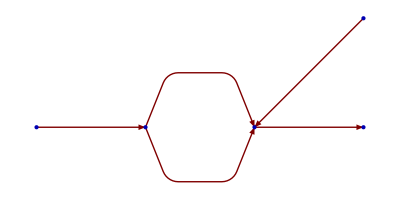
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

(-(ⅈ η^2)/v).ⅈ/(ⅈ ε-2 η^2+k_α^α[h,1].k_α^α[h,1]).(-(ⅈ η^2)/v).ⅈ/(ⅈ ε-2 η^2+k_β^β[h,2].k_β^β[h,2])
(-(ⅈ η^2)/v).ⅈ/(ⅈ ε+k_α^α[χ,1].k_α^α[χ,1]-ξ m_A^2).(-(ⅈ η^2)/v).ⅈ/(ⅈ ε+k_β^β[χ,2].k_β^β[χ,2]-ξ m_A^2)
(ⅈ ξ m_A^2)/v.ⅈ/(ⅈ ε+k_α^α[c̄,1].k_α^α[c̄,1]-ξ m_A^2).(ⅈ ξ m_A^2)/v.ⅈ/(ⅈ ε+k_β^β[c,2].k_β^β[c,2]-ξ m_A^2)
(ⅈ m_A^2)/v.(-ⅈ ξ (1/(k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])-1/(ⅈ ε-ξ m_A^2+k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])) k_μ^μ[A_μ^μ,1] k_ν^ν[A_μ^μ,1]+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_α^α[A_μ^μ,1] k_α^α[A_μ^μ,1])).(ⅈ m_A^2)/v.(-ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2] (1/(k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])-1/(ⅈ ε-ξ m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))
(ⅈ e q_μ^μ[h]).ⅈ/(ⅈ ε+k_α^α[χ,1].k_α^α[χ,1]-ξ m_A^2).(ⅈ e q_ν^ν[h]).(-ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2] (1/(k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])-1/(ⅈ ε-ξ m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))
(-ⅈ e q_μ^μ[χ]).ⅈ/(ⅈ ε+k_α^α[χ,1].k_α^α[χ,1]-ξ m_A^2).(-ⅈ e q_ν^ν[χ]).(-ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2] (1/(k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])-1/(ⅈ ε-ξ m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))

```mathematica
Thread[graph[oneloop]]
PR1[
Column[Thread[tmpm[oneloop]],Frame->All]
]
```

```mathematica
addloopmomentum={
kd[a_][A_,1]->(kd[a][A,1]+jd[a]),
kd[a_][A_,2]->(kd[a][A,2]-jd[a]),
ku[a_][A_,1]->(ku[a][A,1]+ju[a]),
ku[a_][A_,2]->(ku[a][A,2]-ju[a])
}
Do[
PR1[
"Manipulate integrand for type->{1,2,3}: type: ",type,Yield,"POFF",
"Integrand of iM (j[] is loop variable):",
tmp=tmpm[oneloop[[type]]],Yield,
tmp=tmp/.addloopmomentum
],{type,{1,2,3}}
]
"Gamma function approximation using (14.26)."
subGamma=Map[e1426/.n->#/.ε->ϵ&//FullSimplify,{-2,0,1,2,3}]
subGamma[[1]]=Gamma[2-ϵ]->1+γ ϵ

"Gaussian integral substitutions."
sub=e1427hitoshi
sub=sub/.q->ju[α]/.b->2/.a->0/.D->-fD2offset/.ε->0;
sub=sub/.IntegralOp[a_,b_]:>IntegralOpMoveNVarOut[a,b];
sub14270=RuleX[sub,IntegralOp[a_,b_]];
sub=e1427hitoshi;
sub=sub/.q->ju[α]/.b->2/.a->1/.D->-fD2offset/.ε->0;
sub=sub/.IntegralOp[a_,b_]:>IntegralOpMoveNVarOut[a,b];
sub14271=RuleX[sub,IntegralOp[a_,b_]];
sub=e1427hitoshi;
sub=sub/.q->ju[α]/.b->2/.a->2/.D->-fD2offset/.ε->0;
sub=sub/.IntegralOp[a_,b_]:>IntegralOpMoveNVarOut[a,b];
sub14272=RuleX[sub,IntegralOp[a_,b_]];
sub1427Int={sub14270,sub14271,sub14272}//Flatten

sub=e1427hitoshi/.q->ju[α]/.b->2/.a->0/.D->fD2offset;

"Kinematic relations:"
subkinematic:={
ku[a_][b_,1]+ku[a_][b_,2]->ku[a][h,0],
kd[a_][b_,1]+kd[a_][b_,2]->kd[a][h,0],
ku[a_][c,2]+ku[a_][c̄,1]->ku[a][h,0],
kd[a_][c,2]+kd[a_][c̄,1]->kd[a][h,0],
ku[a_][h,0]kd[a_][h,0]->Subscript[m, h] Subscript[m, h],
kd[a_][h,0].ku[a_][h,0]->Subscript[m, h] Subscript[m, h],
kd[a_][χ,1].ku[a_][χ,1]->0,
ku[a_][particles[[2]],2]->ku[a][h,0]-ku[a][particles[[1]],1],
kd[a_][particles[[2]],2]->kd[a][h,0]-kd[a][particles[[1]],1]
};
subloopkinematics={ku[a_][b_,1]->0,kd[a_][b_,1]->0};

subvertexq={qu[a_][b_]:>ku[a][b,0]/;b===h,
qu[a_][b_]:>ku[a][b,1]/;b===χ};

(*numerator substitutions for even loop integration.*)
subjksym={
ju[a_].kd[a_][c_,cn_]jd[b_].ku[b_][d_,dn_]:>ju[α].jd[α]kd[a][c,cn].ku[a][d,dn]/dim,
ju[a_].kd[a_][c_,cn_]ju[b_].kd[b_][d_,dn_]:>ju[α].jd[α]kd[a][c,cn].ku[a][d,dn]/dim,
jd[a_].ku[a_][c_,cn_]jd[b_].ku[b_][d_,dn_]:>ju[α].jd[α]kd[a][c,cn].ku[a][d,dn]/dim,
(ju[a_].kd[a_][c_,cn_])^2:>ju[α].jd[α]kd[a][c,cn].ku[a][c,cn]/dim,
(jd[a_].ku[a_][c_,cn_])^2:>ju[α].jd[α]kd[a][c,cn].ku[a][c,cn]/dim
};
(*converts bi-vector index contractions into Dot[] expression, contracts with metric tensor, *)
subregj={
jd[a_]ku[a_][A_,n_]:>ju[α].kd[α][A,n],
HoldPattern[jd[a_].ku[a_][A_,n_]]:>ju[α].kd[α][A,n],
kd[a_][B_,nb_]ku[a_][A_,na_]:>ku[α][A,na].kd[α][B,nb],
jd[a_]ju[a_]:>ju[α].jd[α],
ju[a_]kd[a_][A_,n_]:>ju[α].kd[α][A,n],
guu[m_,n_]kd[n_][a__]->ku[m][a],
gdd[m_,n_]ku[n_][a__]->kd[m][a],
guu[m_,n_]kd[m_][a__]->ku[n][a],
gdd[m_,n_]ku[m_][a__]->kd[n][a]
};
contractg={
guu[m_,n_]kd[n_][a__]->ku[m][a],
gdd[m_,n_]ku[n_][a__]->kd[m][a],
guu[m_,n_]kd[m_][a__]->ku[n][a],
gdd[m_,n_]ku[m_][a__]->kd[n][a],
guu[m_,n_]jd[m_]->ju[n],
gdd[m_,n_]ju[m_]->jd[n],
guu[n_,m_]jd[m_]->ju[n],
gdd[n_,m_]ju[m_]->jd[n],
gdu[n_,n_]|gud[n_,n_]->dim
};
contract2Dot={
ku[a_][b_,c_]kd[a_][d_,e_]->ku[α][b,c].kd[α][d,e],
ju[a_]kd[a_][d_,e_]->ju[α].kd[α][d,e],
jd[a_]ku[a_][d_,e_]->ju[α].kd[α][d,e],
jd[a_]ju[a_]:>ju[α].jd[α]
};

UpDownOrder={
ku[a_][A__].kd[a_][B__]:>kd[a][A].ku[a][B]/;OrderedQ[{{B},{A}}],
kd[a_][B__].ku[a_][A__]:>kd[a][A].ku[a][B]/;OrderedQ[{{B},{A}}],
HoldPattern[jd[a_].ku[a_][A_,n_]]:>ju[α].kd[α][A,n],
jd[a_].ku[a_][A_,n_]:>ju[α].kd[α][A,n]
};
(* Reduces equation to decay kinematics. k[,0]->{Subscript[m, h],0,0,0}. *)
DecayKinematics[exp_]:=Module[{tmp=exp,simplify={simpleDot,commuteDot}//Flatten},
DotExpandMode[True];

tmp=tmp/.contract2Dot//.simplify//.subkinematic//.simplify//.subjksym//.simplify//.UpDownOrder//.simpleDot;
tmp=DotKeepPattern[{Tensor[_,_,_],Tensor[_,_,_][__]}][tmp];
tmp=tmp//.contract2Dot/.subkinematic/.subloopkinematics//.simplify//.UpDownOrder//Expand;
tmp=DotKeepPattern[{Tensor[_,_,_],Tensor[_,_,_][__]}][tmp];
tmp=tmp//.simplify//.UpDownOrder//.subjksym//.simplify;
DotExpandMode[False];
tmp
];
```

{k_a_^a_[A_,1]→j_a^a+k_a^a[A,1],k_a_^a_[A_,2]→-j_a^a+k_a^a[A,2],k_a_^a_[A_,1]→j_a^a+k_a^a[A,1],k_a_^a_[A_,2]→-j_a^a+k_a^a[A,2]}

Manipulate integrand for type->{1,2,3}: type: 1
→

Manipulate integrand for type->{1,2,3}: type: 2
→

Manipulate integrand for type->{1,2,3}: type: 3
→

Gamma function approximation using (14.26).

{Gamma[2+ϵ]:>(1/ϵ-γ+∑_(k=1)^-2 1/k)/((-1)^2 (-2)!),Gamma[ϵ]:>((-1)^0 (1/ϵ-γ+∑_(k=1)^0 1/k))/(0!),Gamma[-1+ϵ]:>((-1)^1 (1/ϵ-γ+∑_(k=1)^1 1/k))/(1!),Gamma[-2+ϵ]:>((-1)^2 (1/ϵ-γ+∑_(k=1)^2 1/k))/(2!),Gamma[-3+ϵ]:>((-1)^3 (1/ϵ-γ+∑_(k=1)^3 1/k))/(3!)}

Gamma[2-ϵ]→1+γ ϵ

Gaussian integral substitutions.

∫_{q} [(q^2)^a (-D+q^2-ⅈ ε)^-b]→(ⅈ (-1)^(a+b) D^(a-b+d/2) π^(d/2) Gamma[-a+b-d/2] Gamma[a+d/2])/(Gamma[b] Gamma[d/2])

{∫_{j_α^α} [1/((fD2offset+(j_α^α)^2)^2)]→(ⅈ (-fD2offset)^(d/2) π^(d/2) Gamma[2-d/2])/fD2offset^2,∫_{j_α^α} [((j_α^α)^2)/((fD2offset+(j_α^α)^2)^2)]→(ⅈ (-fD2offset)^(d/2) π^(d/2) Gamma[1-d/2] Gamma[1+d/2])/(fD2offset Gamma[d/2]),∫_{j_α^α} [((j_α^α)^4)/((fD2offset+(j_α^α)^2)^2)]→(ⅈ (-fD2offset)^(d/2) π^(d/2) Gamma[2+d/2] Gamma[-d/2])/Gamma[d/2]}

Kinematic relations:

```mathematica
Clear[iM];
iM=Range[6];
Do[
PR1[
"Manipulate integrand for type->{1,2,3}: type: ",type,yield,particles=particlename[oneloop[[type]]],Yield,
"POFF",
"Integrand of iM (j[] is loop variable):",
tmp=tmpm[oneloop[[type]]],Yield,
tmp=tmp/.addloopmomentum,Yield,
"where ",var=ju[α]," is loop momentum.",Yield,
"Vertex factors",yield,
tmpc=tmp[[1]]tmp[[3]],Yield,
"Propagator term:",yield,
tmp=Delete[tmp,{{1},{3}}],Yield,
"Feynman parametric, x[], factors",Yield,
feynmanp=FactorDotFeynman[tmp],Yield,
"Change j[] variable to complete square.",Yield,
feynmanp=feynmanp/.jd[α]->var;
sq=CompleteSquare1[feynmanp,var];
feynmanp[[2]]=var^2+fD2offset;
"Parametrized integrand: ",yield,
tmp=feynmanp[[1]]Power[feynmanp[[2]],-feynmanp[[3]]],Yield,

"PON",
"Insert into Integral -> iM:",Yield,
tmp=IntegralOp[xF[2],(feynmanp[[3]]) DiracDelta[1-feynmanp[[4]]] IntegralOp[{{var}},tmp]];
tmp=tmp/.IntegralOp[a_,b_]:>IntegralOpMoveNVarOut[a,b]/;a==={{ju[α]}},
New,"Simplify offset term. ",
"POFF",
tmpoffset=sq[[3]]/.a_ a_:>a (a//RaiseIndex[α,α])//Expand,Yield,
tmpoffset[[2]]=tmpoffset[[2]]//SimplifyTensorSum//UpDownAdjust,Yield,
"PON",
tmpoffset,
"POFF",
New,"Substitute (14.27)->Γ and offset. iM: ",Yield,
tmp=tmp/.(sub1427Int/.ε->0)/.tmpoffset(*ε reinstated by offset*),Yield,
"Integrate out Feynman parameters.",Yield,
tmp=tmp/.IntegralOp[a_,b_]:>evalDeltaIntOver[IntegralOp[a,b],x[2]],Yield,
tmp=tmp/.IntegralOp[a_,b_]:>IntegralOpMoveNVarOut[a,b],Yield,

"PON",
"Dimensional regularization: ",sub=d->4-ϵ 2,Yield,
tmp=tmp/.sub//FullSimplify,Yield,
tmp=tmp//.subkinematic,
New,"Hitoshi evaluates Imaginary part of the loop diagram.  Branch cut when arguement of Log[] is <=0. ",Yield,
tmpHito=tmp//ExtractIntegrand;
"Series expansion of integrand:",Yield,
tmpintg=Series[tmpHito[[2,1]],{ϵ,0,1}]//Normal,Yield,
tmpPV=ReplacePart[tmp,tmpHito[[1,1]]->tmpintg],Yield,
"A branch cut defined by the arguement of Log[] <=0.",Yield,
tmpL=ExtractPattern[tmpintg,Log[_]]/.Log->List//Flatten//First;
tmpL=(tmpL/.ε->0)<=0//Simplify;
negcond=Reduce[tmpL&&ξ>0&&Subscript[m, h]>0&&Subscript[m, A]>0&&η>0,{x[1]},Reals],back,
"Sort out the appropriate range for x[1]. ",
CR["Complete integration."],

New,
"iM:",oneloop[[type]],yield,
tmp=tmpc tmp/.subGamma;
iM[[type]]=tmp
],
{type,{1,2,3}}]
```

Manipulate integrand for type->{1,2,3}: type: 1 ⟶ {h,h}
→ Insert into Integral -> iM:
→ ∫_({x[1],0,1}
{x[2],0,1}) [-2 DiracDelta[-1+x[1]+x[2]] ∫_{j_α^α} [1/((fD2offset+(j_α^α)^2)^2)]]
● Simplify offset term. fD2offset→ⅈ ε-2 η^2+x[1] k_α^α[h,1] k_α^α[h,1]-x[1]^2 k_α^α[h,1] k_α^α[h,1]+x[1] k_α^α[h,2] k_α^α[h,1]-x[1]^2 k_α^α[h,2] k_α^α[h,1]+x[1] k_α^α[h,1] k_α^α[h,2]-x[1]^2 k_α^α[h,1] k_α^α[h,2]+x[1] k_α^α[h,2] k_α^α[h,2]-x[1]^2 k_α^α[h,2] k_α^α[h,2]Dimensional regularization: d→4-2 ϵ
→ -2 ⅈ π^(2-ϵ) Gamma[ϵ] ∫_{x[1],0,1} [(-ⅈ ε+2 η^2+(-1+x[1]) x[1] (k_α^α[h,1]+k_α^α[h,2]) (k_α^α[h,1]+k_α^α[h,2]))^-ϵ]
→ -2 ⅈ π^(2-ϵ) Gamma[ϵ] ∫_{x[1],0,1} [(-ⅈ ε+2 η^2+m_h^2 (-1+x[1]) x[1])^-ϵ]
● Hitoshi evaluates Imaginary part of the loop diagram.  Branch cut when arguement of Log[] is <=0. 
→ Series expansion of integrand:
→ 1-ϵ Log[-ⅈ ε+2 η^2+m_h^2 (-1+x[1]) x[1]]
→ -2 ⅈ π^(2-ϵ) Gamma[ϵ] ∫_{x[1],0,1} [1-ϵ Log[-ⅈ ε+2 η^2+m_h^2 (-1+x[1]) x[1]]]
→ A branch cut defined by the arguement of Log[] <=0.
→ m_h>0&&((0<η<(√(m_h^2))/(2 √2)&&m_A>0&&ξ>0&&1/2-1/2 √((-8 η^2+m_h^2)/m_h^2)≤x[1]≤1/2+1/2 √((-8 η^2+m_h^2)/m_h^2))||(η==(√(m_h^2))/(2 √2)&&m_A>0&&ξ>0&&x[1]==1/2-1/2 √((-8 η^2+m_h^2)/m_h^2))) ⟵Sort out the appropriate range for x[1]. Complete integration.
● iM:2 ⟶ (2 ⅈ π^(2-ϵ) (-γ+1/ϵ) η^4 ∫_{x[1],0,1} [(-ⅈ ε+2 η^2+m_h^2 (-1+x[1]) x[1])^-ϵ])/v^2

Manipulate integrand for type->{1,2,3}: type: 2 ⟶ {χ,χ}
→ Insert into Integral -> iM:
→ ∫_({x[1],0,1}
{x[2],0,1}) [-2 DiracDelta[-1+x[1]+x[2]] ∫_{j_α^α} [1/((fD2offset+(j_α^α)^2)^2)]]
● Simplify offset term. fD2offset→ⅈ ε-ξ m_A^2+x[1] k_α^α[χ,1] k_α^α[χ,1]-x[1]^2 k_α^α[χ,1] k_α^α[χ,1]+x[1] k_α^α[χ,2] k_α^α[χ,1]-x[1]^2 k_α^α[χ,2] k_α^α[χ,1]+x[1] k_α^α[χ,1] k_α^α[χ,2]-x[1]^2 k_α^α[χ,1] k_α^α[χ,2]+x[1] k_α^α[χ,2] k_α^α[χ,2]-x[1]^2 k_α^α[χ,2] k_α^α[χ,2]Dimensional regularization: d→4-2 ϵ
→ -2 ⅈ π^(2-ϵ) Gamma[ϵ] ∫_{x[1],0,1} [(-ⅈ ε+ξ m_A^2+(-1+x[1]) x[1] (k_α^α[χ,1]+k_α^α[χ,2]) (k_α^α[χ,1]+k_α^α[χ,2]))^-ϵ]
→ -2 ⅈ π^(2-ϵ) Gamma[ϵ] ∫_{x[1],0,1} [(-ⅈ ε+ξ m_A^2+m_h^2 (-1+x[1]) x[1])^-ϵ]
● Hitoshi evaluates Imaginary part of the loop diagram.  Branch cut when arguement of Log[] is <=0. 
→ Series expansion of integrand:
→ 1-ϵ Log[-ⅈ ε+ξ m_A^2+m_h^2 (-1+x[1]) x[1]]
→ -2 ⅈ π^(2-ϵ) Gamma[ϵ] ∫_{x[1],0,1} [1-ϵ Log[-ⅈ ε+ξ m_A^2+m_h^2 (-1+x[1]) x[1]]]
→ A branch cut defined by the arguement of Log[] <=0.
→ m_A>0&&m_h>0&&((0<ξ<m_h^2/(4 m_A^2)&&η>0&&1/2-1/2 √((-4 ξ m_A^2+m_h^2)/m_h^2)≤x[1]≤1/2+1/2 √((-4 ξ m_A^2+m_h^2)/m_h^2))||(ξ==m_h^2/(4 m_A^2)&&η>0&&x[1]==1/2-1/2 √((-4 ξ m_A^2+m_h^2)/m_h^2))) ⟵Sort out the appropriate range for x[1]. Complete integration.
● iM:4 ⟶ (2 ⅈ π^(2-ϵ) (-γ+1/ϵ) η^4 ∫_{x[1],0,1} [(-ⅈ ε+ξ m_A^2+m_h^2 (-1+x[1]) x[1])^-ϵ])/v^2

Manipulate integrand for type->{1,2,3}: type: 3 ⟶ {c̄,c}
→ Insert into Integral -> iM:
→ ∫_({x[1],0,1}
{x[2],0,1}) [-2 DiracDelta[-1+x[1]+x[2]] ∫_{j_α^α} [1/((fD2offset+(j_α^α)^2)^2)]]
● Simplify offset term. fD2offset→ⅈ ε-ξ m_A^2+x[1] k_α^α[c,2] k_α^α[c,2]-x[1]^2 k_α^α[c,2] k_α^α[c,2]+x[1] k_α^α[c̄,1] k_α^α[c,2]-x[1]^2 k_α^α[c̄,1] k_α^α[c,2]+x[1] k_α^α[c,2] k_α^α[c̄,1]-x[1]^2 k_α^α[c,2] k_α^α[c̄,1]+x[1] k_α^α[c̄,1] k_α^α[c̄,1]-x[1]^2 k_α^α[c̄,1] k_α^α[c̄,1]Dimensional regularization: d→4-2 ϵ
→ -2 ⅈ π^(2-ϵ) Gamma[ϵ] ∫_{x[1],0,1} [(-ⅈ ε+ξ m_A^2+(-1+x[1]) x[1] (k_α^α[c,2]+k_α^α[c̄,1]) (k_α^α[c,2]+k_α^α[c̄,1]))^-ϵ]
→ -2 ⅈ π^(2-ϵ) Gamma[ϵ] ∫_{x[1],0,1} [(-ⅈ ε+ξ m_A^2+m_h^2 (-1+x[1]) x[1])^-ϵ]
● Hitoshi evaluates Imaginary part of the loop diagram.  Branch cut when arguement of Log[] is <=0. 
→ Series expansion of integrand:
→ 1-ϵ Log[-ⅈ ε+ξ m_A^2+m_h^2 (-1+x[1]) x[1]]
→ -2 ⅈ π^(2-ϵ) Gamma[ϵ] ∫_{x[1],0,1} [1-ϵ Log[-ⅈ ε+ξ m_A^2+m_h^2 (-1+x[1]) x[1]]]
→ A branch cut defined by the arguement of Log[] <=0.
→ m_A>0&&m_h>0&&((0<ξ<m_h^2/(4 m_A^2)&&η>0&&1/2-1/2 √((-4 ξ m_A^2+m_h^2)/m_h^2)≤x[1]≤1/2+1/2 √((-4 ξ m_A^2+m_h^2)/m_h^2))||(ξ==m_h^2/(4 m_A^2)&&η>0&&x[1]==1/2-1/2 √((-4 ξ m_A^2+m_h^2)/m_h^2))) ⟵Sort out the appropriate range for x[1]. Complete integration.
● iM:5 ⟶ (2 ⅈ π^(2-ϵ) (-γ+1/ϵ) ξ^2 ∫_{x[1],0,1} [(-ⅈ ε+ξ m_A^2+m_h^2 (-1+x[1]) x[1])^-ϵ] m_A^4)/v^2

```mathematica
Do[
PR1[
particles=particlename[oneloop[[type]]];
"Manipulate integrand for type->{4,5,6}, type: ",type,back,particles,Yield,
tmp=tmpm[oneloop[[type]]];Yield;
tmp=tmp/.subvertexq//ExpandAll;
Column[term=Apply[List,tmp],Frame->All]
]
nterms=Length[term];
termlist=Range[nterms];

sumterms=0;
Do[
PR1[
"Evaluate vertex.propagator.vertex.propagator term ",termn,Yield,
tmp=term[[termn]],
If[FreeQ[tmp,ξ],"⟵physical","⟵unphysical"],Yield,
"POFF",
"Pick out propagators for Feynman parameterization.",Yield,
tmpc=Pick[tmp,{1,0,1,0},1]/.Dot->Times;
tmpp=Pick[tmp,{1,0,1,0},0],check,Yield,
feynmanp=FactorDotFeynman[tmpp],Yield,

"Add loop momentum and Feynman parameterization.";
feynmanp=feynmanp/.addloopmomentum,Yield,
var=ju[α];
feynmanp=feynmanp/.jd[α]->var;
sq=CompleteSquare1[feynmanp,var];
feynmanp[[2]]=var^2+fD2offset;

"Numerator adjust k's and j's.",Yield,
tNumerator=feynmanp[[1]](tmpc/.addloopmomentum),Yield,
"Factor out constants for new coefficient and momentum expression.",Yield,
tNumerator=tNumerator//Simplify,Yield,
tmpc=DeleteCases[tNumerator,Except[ξ|Subscript[m, A]^_|v^_|v|e|e^_]],back,"coefficient",Yield,
tNumerator=tNumerator/tmpc//Simplify//Expand,Yield,

"Insert definition of projection operator.",Yield,
subPux=subPu/.{(1/(k k))->1/(ku[α][Au[μ],2].kd[α][Au[μ],2]),
ku[m_]->ku[m][Au[μ],2]
},check,Yield,
subPdx=subPux//LowerIndex[μ,μ]//LowerIndex[ν,ν],Yield,
subPdx=subPdx/.Ad[m_]->Au[m],Yield,
tNumerator=tNumerator/.subPux/.subPdx//Expand//MetricSimplify[g],Yield,
tNumerator=tNumerator//.subregj//Expand,Yield,

"Shift numerator loop momentum, j, by offset: ",
shift=sq[[4]]//RaiseIndex[α,α]//Simplify;
shift2={shift[[2]],shift[[2]]//LowerIndex[α,α]},Yield,
tNumerator=tNumerator/.shift2//Expand,Yield,
tNumerator=tNumerator/.{ju[a_]->X ju[a],jd[a_]->X jd[a]}//Expand,Yield,
tNumerator=tNumerator//.simpleDot,Yield,
tNumerator=DotKeepPattern[{Tensor[_,_,_],Tensor[_,_,_][__]}][tNumerator],Yield,

"Only keep even powers of j and apply Lorentz symmetry relationship for integrals.",Yield,
tNumerator=CoefficientList[tNumerator,X],check,Yield,

tNumerator=Delete[tNumerator,List/@Range[2,Length[tNumerator],2]],Yield,
tNumerator=DecayKinematics[tNumerator],Yield,
tNumerator=tNumerator/.{}->{0};


"There should be no j.k terms after here.",Yield,
Column[tNumerator,Frame->All],check,Yield,
"PON",
"Numerator for even powers of loop momenta, j:",Yield,
Column[tmpNj=CoefficientList[tNumerator,(jd[α].ju[α]/.commuteDot)],Frame->All],Yield,
"POFF",

New,
"Construct integral with denominator and j.j^n terms and substitute 14.27 for Gaussian form.",Yield,
ConstructIntegral[jj_,tmpx_]:=Module[{tmp,tmpI,DEBUG=0},
IfDEBUG["ConstructIntegral",DEBUG>0,{jj,tmpx},"input"];
feynmanp[[1]]=tmpx;
tmp= Power[feynmanp[[2]],-feynmanp[[3]]];(*Denominator*)
tmp=tmp//.subregj/.contract2Dot;
tmpI=(IntegralOp[{{var}},jj tmp]//.sub1427Int);
IfDEBUG["ConstructIntegral",DEBUG>0,{tmpI},"tmpI"];
tmp=IntegralOp[xF[2],(feynmanp[[3]])! DiracDelta[1-feynmanp[[4]]]tmpI feynmanp[[1]]];
If[tmpx==0,tmp=0];
IfDEBUG["ConstructIntegral",DEBUG>0,{tmp},"output"];
tmp
];

"POFF",
For[i=1,i<=Length[tmpNj],i++,tmpNjj=tmpNj[[i]];
tmpNjji=Map[ConstructIntegral[(ju[α]ju[α])^(#-1),tmpNjj[[#]]]&,Range[Length[tmpNjj]]];
tmpNj[[i]]=Apply[Plus,tmpNjji]
];
tmp=Apply[Plus,tmpNj],check,Yield,
"POFF",
"Simplify offset and add.",Yield,
tmpoffset=sq[[3]]/.Power[Plus[a__],2]:>(a//RaiseIndex[α,α])(a//LowerIndex[α,α])//Expand,Yield,
tmpoffset=DecayKinematics[tmpoffset],Yield,
tmp=tmp//.tmpoffset,Yield,

tmp=DecayKinematics[tmp],check,Yield,
tmp=tmp/.IntegralOp[a_,b_]:>evalDeltaIntOver[IntegralOp[a,b],x[2]],Yield,
tmp=tmp/.IntegralOp[a_,b_]:>IntegralOpMoveNVarOut[a,b],Yield,
tmp=tmpc Apply[Plus,tmp]/.ε->0//Simplify,check,Yield,

sumterms+=tmp;
],{termn,1,nterms}
];
subd=d->4-ϵ 2;
sumterms=sumterms/.ε->0/.subd//.subkinematic//FullSimplify;

DotExpandMode[True];
PR1[
"iM:",
oneloop[[type]],Yield,
"POFF",
sub=particles,Yield,
sub=ku[a_][sub[[2]],2]->ku[a][h,0]-ku[a][sub[[1]],1],Yield,
sub={sub,(sub//LowerIndex[a,a])},Yield,
sumterms=sumterms//Expand,check,Yield,
"PON",
iM[[type]]=sumterms//DecayKinematics
]
,{type,{6}}
];
```

Manipulate integrand for type->{4,5,6}, type: 6 ⟵{χ,A_μ^μ}
→ (-ⅈ e q_μ^μ[χ]).ⅈ/(ⅈ ε+k_α^α[χ,1].k_α^α[χ,1]-ξ m_A^2).(-ⅈ e q_ν^ν[χ]).(-ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2] (1/(k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])-1/(ⅈ ε-ξ m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2]))
→ -ⅈ e k_μ^μ[χ,1]
ⅈ/(ⅈ ε+k_α^α[χ,1].k_α^α[χ,1]-ξ m_A^2)
-ⅈ e k_ν^ν[χ,1]
-(ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2])/(k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])+(ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2])/(ⅈ ε-ξ m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])

Pick::incomp: Expressions -ⅈ e InterpretationBox[k_StyleBox[ and {1, 0, 1, 0} have incompatible shapes.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 2} and {2, 3} of MapThread[#3 #1/#2 &, {{x[1], x[2], x[3]}, {-ⅈ e InterpretationBox[k_StyleBox[; dimensions are {3} and {4}.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[#1 → #2 &, {{c$130471, b$130471, a$130471}, {UpDownAdjust[SimplifyTensorSum[{{Plus[« 2 »], Plus[« 2 »], Plus[« 4 »]}, {Plus[« 2 »], {« 4 »}, « 1 » &}, {{« 3 »}, {« 3 »}, {« 3 »}, {« 3 »}}}]]}}]; dimensions are {3} and {1}.

ReplaceAll::reps: {MapThread[#1 → #2 &, {{c$130471, b$130471, a$130471}, {UpDownAdjust[SimplifyTensorSum[{{« 3 »}, {« 3 »}, {« 4 »}}]]}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Pick::incomp: Expressions -ⅈ e (InterpretationBox[j_StyleBox[ and {1, 0, 1, 0} have incompatible shapes.

General::stop: Further output of Pick will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {e^4 Pick[-ⅈ e (InterpretationBox[j_« 1 » « 1 », Tensor[j, List[Skeleton[1]], List[Skeleton[1]]], Rule[Editable, False], Rule[BaseStyle, List[Rule[AutoMultiplicationSymbol, False]]]] + InterpretationBox[k_« 1 » « 1 », Tensor[k, List[Skeleton[1]], List[Skeleton[1]]], Rule[Editable, False], Rule[BaseStyle, List[Rule[AutoMultiplicationSymbol, False]]]][χ, 1]), {1, 0, 1, 0}, 1] (InterpretationBox[j_StyleBox[ cannot be combined.

Thread::tdlen: Objects of unequal length in « 1 » {} cannot be combined.

General::stop: Further output of Thread will be suppressed during this calculation.

Part::partw: Part 4 of {fD2all → -Power[« 2 »] + 4 a$130471 c$130471/4 a$130471 + a$130471 (Times[« 3 »] + InterpretationBox[« 3 », Tensor[Skeleton[3]], Rule[Editable, False]])^2, fD2 → a$130471 (1/2 Power[« 2 »] b$130471 + InterpretationBox[j_« 1 » « 1 », Tensor[j, List[Skeleton[1]], List[Skeleton[1]]], Rule[Editable, False], Rule[BaseStyle, List[Rule[AutoMultiplicationSymbol, False]]]])^2, fD2offset → -b$130471^2 + 4 a$130471 c$130471/4 a$130471, varshift → InterpretationBox[j_StyleBox[ does not exist.

ReplaceAll::reps: {4, 4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll will be suppressed during this calculation.

Part::partw: Part 3 of {fD2all → -Power[« 2 »] + 4 a$130471 c$130471/4 a$130471 + a$130471 (Times[« 3 »] + InterpretationBox[« 3 », Tensor[Skeleton[3]], Rule[Editable, False]])^2, fD2 → a$130471 (1/2 Power[« 2 »] b$130471 + InterpretationBox[j_« 1 » « 1 », Tensor[j, List[Skeleton[1]], List[Skeleton[1]]], Rule[Editable, False], Rule[BaseStyle, List[Rule[AutoMultiplicationSymbol, False]]]])^2, fD2offset → -b$130471^2 + 4 a$130471 c$130471/4 a$130471, varshift → InterpretationBox[j_StyleBox[ does not exist.

Part::partw: Part 3 of {fD2all → -Power[« 2 »] + 4 a$130471 c$130471/4 a$130471 + a$130471 (1/2 Power[« 2 »] b$130471 + InterpretationBox[j_« 1 » « 1 », Tensor[j, List[Skeleton[1]], List[Skeleton[1]]], Rule[Editable, False], Rule[BaseStyle, List[Rule[AutoMultiplicationSymbol, False]]]]) (1/2 Power[« 2 »] b$130471 + InterpretationBox[j_« 1 » « 1 », Tensor[j, List[Skeleton[1]], List[Skeleton[1]]], Rule[Editable, False], Rule[BaseStyle, List[Rule[AutoMultiplicationSymbol, False]]]]), fD2 → a$130471 (b$130471/2 a$130471 + InterpretationBox[j_α StyleBox[ does not exist.

General::stop: Further output of Part will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[#1 → #2 &, {{c$130471, b$130471, a$130471}, {UpDownAdjust[SimplifyTensorSum[{{Plus[« 2 »], Plus[« 2 »], Plus[« 4 »]}, {Plus[« 2 »], {« 4 »}, « 1 » &}, {{« 3 »}, {« 3 »}, {« 3 »}, {« 3 »}}}]]}}]; dimensions are {3} and {1}.

General::stop: Further output of MapThread will be suppressed during this calculation.

ReplaceRepeated::reps: {({fD2all → 1/4 Power[« 2 »] Plus[« 2 »] + a$130471 Plus[« 2 »] Plus[« 2 »], fD2 → a$130471 (Times[« 3 »] + InterpretationBox[« 3 », Tensor[Skeleton[3]], Rule[Editable, False]]) (Times[« 3 »] + InterpretationBox[« 3 », Tensor[Skeleton[3]], Rule[Editable, False]]), fD2offset → Times[« 2 »] + Times[« 3 »]/4 a$130471, varshift → InterpretationBox[j_« 1 » « 1 », Tensor[j, List[Skeleton[1]], List[Skeleton[1]]], Rule[Editable, False], Rule[BaseStyle, List[Rule[AutoMultiplicationSymbol, False]]]] → Times[« 3 »] + InterpretationBox[« 3 », Tensor[Skeleton[3]], Rule[Editable, False]]}/. MapThread[#1 → #2 &, {{c$130471, b$130471, a$130471}, {« 1 »}}]) ⟦ 3 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated will be suppressed during this calculation.

Evaluate vertex.propagator.vertex.propagator term 1
→ -ⅈ e k_μ^μ[χ,1]⟵physical
→ Numerator for even powers of loop momenta, j:
→ {{0} {-ⅈ e^4 X^5 (j_μ^μ)^4,0,0}/.{4,4}}
→

Evaluate vertex.propagator.vertex.propagator term 2
→ ⅈ/(ⅈ ε+k_α^α[χ,1].k_α^α[χ,1]-ξ m_A^2)⟵unphysical
→ Numerator for even powers of loop momenta, j:
→ {{0} {Pick[ⅈ/(ⅈ ε-ξ m_A^2+X^2 j_α^α j_α^α),{1,0,1,0},1],0,0}/.{4,4}}
→

Evaluate vertex.propagator.vertex.propagator term 3
→ -ⅈ e k_ν^ν[χ,1]⟵physical
→ Numerator for even powers of loop momenta, j:
→ {{0} {-ⅈ e^4 X^5 (j_ν^ν)^4,0,0}/.{4,4}}
→

Evaluate vertex.propagator.vertex.propagator term 4
→ -(ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2])/(k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])+(ⅈ ξ k_μ^μ[A_μ^μ,2] k_ν^ν[A_μ^μ,2])/(ⅈ ε-ξ m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])+(ⅈ P_μν^μν[k])/(ⅈ ε-m_A^2+k_β^β[A_μ^μ,2] k_β^β[A_μ^μ,2])⟵unphysical
→ Numerator for even powers of loop momenta, j:
→ {{0} {(Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^4)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4-(4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^3 k_μ^μ[h,0] k_ν^ν[h,0])/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4)+(6 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/(m_h^4 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4)-(4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/(m_h^6 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4)+(Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^4)/(m_h^8 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4)+(X^8 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (j_ν^ν)^4)/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4-(4 X^7 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^4 k_μ^μ[h,0])/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4+(6 X^6 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^4 (k_μ^μ[h,0])^2)/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4-(4 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^4 (k_μ^μ[h,0])^3)/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4+(X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^4 (k_μ^μ[h,0])^4)/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4-(4 X^7 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (j_ν^ν)^3 k_ν^ν[h,0])/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4+(16 X^6 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^3 k_μ^μ[h,0] k_ν^ν[h,0])/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4-(24 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^3 (k_μ^μ[h,0])^2 k_ν^ν[h,0])/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4+(16 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^3 (k_μ^μ[h,0])^3 k_ν^ν[h,0])/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4-(4 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^3 (k_μ^μ[h,0])^4 k_ν^ν[h,0])/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4+(6 X^6 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (j_ν^ν)^2 (k_ν^ν[h,0])^2)/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4-(24 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^2 k_μ^μ[h,0] (k_ν^ν[h,0])^2)/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4+(36 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4-(24 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^2 (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4+(6 X^2 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^2 (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^2)/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4-(4 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 j_ν^ν (k_ν^ν[h,0])^3)/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4+(16 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 j_ν^ν k_μ^μ[h,0] (k_ν^ν[h,0])^3)/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4-(24 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4+(16 X^2 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4-(4 X ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_ν^ν (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^3)/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4+(X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (k_ν^ν[h,0])^4)/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4-(4 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 k_μ^μ[h,0] (k_ν^ν[h,0])^4)/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4+(6 X^2 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^4)/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4-(4 X ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^4)/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4+(ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^4)/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^4-(4 X^6 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^3 (j_ν^ν)^3)/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)+(12 X^5 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 (j_ν^ν)^3 k_μ^μ[h,0])/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)-(12 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (j_ν^ν)^3 (k_μ^μ[h,0])^2)/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)+(4 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_ν^ν)^3 (k_μ^μ[h,0])^3)/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)+(12 X^5 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^3 (j_ν^ν)^2 k_ν^ν[h,0])/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)-(36 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 (j_ν^ν)^2 k_μ^μ[h,0] k_ν^ν[h,0])/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)+(4 X^6 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^3 k_μ^μ[h,0] k_ν^ν[h,0])/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)+(36 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (j_ν^ν)^2 (k_μ^μ[h,0])^2 k_ν^ν[h,0])/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)-(12 X^5 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^3 (k_μ^μ[h,0])^2 k_ν^ν[h,0])/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)-(12 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_ν^ν)^2 (k_μ^μ[h,0])^3 k_ν^ν[h,0])/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)+(12 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^3 (k_μ^μ[h,0])^3 k_ν^ν[h,0])/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)-(4 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^3 (k_μ^μ[h,0])^4 k_ν^ν[h,0])/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)-(12 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^3 j_ν^ν (k_ν^ν[h,0])^2)/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)+(36 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 j_ν^ν k_μ^μ[h,0] (k_ν^ν[h,0])^2)/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)-(12 X^5 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^2 k_μ^μ[h,0] (k_ν^ν[h,0])^2)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)-(36 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)+(36 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)+(12 X ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)-(36 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^2 (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)+(12 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^2 (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^2)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)+(4 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^3 (k_ν^ν[h,0])^3)/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)-(12 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 k_μ^μ[h,0] (k_ν^ν[h,0])^3)/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)+(12 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 j_ν^ν k_μ^μ[h,0] (k_ν^ν[h,0])^3)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)+(12 X ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)-(36 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)-(4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)+(36 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)-(12 X ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_ν^ν (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^3)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)-(4 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 k_μ^μ[h,0] (k_ν^ν[h,0])^4)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)+(12 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^4)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)-(12 X ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^4)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)+(4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^4)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3)+(6 X^4 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 (j_μ^μ)^2 (j_ν^ν)^2)/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)-(12 X^3 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 j_μ^μ (j_ν^ν)^2 k_μ^μ[h,0])/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)+(6 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 (j_ν^ν)^2 (k_μ^μ[h,0])^2)/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)-(12 X^3 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 (j_μ^μ)^2 j_ν^ν k_ν^ν[h,0])/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)+(24 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 j_μ^μ j_ν^ν k_μ^μ[h,0] k_ν^ν[h,0])/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)-(12 X^4 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 (j_ν^ν)^2 k_μ^μ[h,0] k_ν^ν[h,0])/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)-(12 X ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 j_ν^ν (k_μ^μ[h,0])^2 k_ν^ν[h,0])/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)+(24 X^3 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (j_ν^ν)^2 (k_μ^μ[h,0])^2 k_ν^ν[h,0])/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)-(12 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_ν^ν)^2 (k_μ^μ[h,0])^3 k_ν^ν[h,0])/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)+(6 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 (j_μ^μ)^2 (k_ν^ν[h,0])^2)/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)-(12 X ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 j_μ^μ k_μ^μ[h,0] (k_ν^ν[h,0])^2)/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)+(24 X^3 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 j_ν^ν k_μ^μ[h,0] (k_ν^ν[h,0])^2)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)+(6 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)-(48 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)+(6 X^4 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/(m_h^4 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)+(24 X ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)-(12 X^3 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^2 (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/(m_h^4 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)+(6 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^2 (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^2)/(m_h^4 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)-(12 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 k_μ^μ[h,0] (k_ν^ν[h,0])^3)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)+(24 X ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)-(12 X^3 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/(m_h^4 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)-(12 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)+(24 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/(m_h^4 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)-(12 X ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_ν^ν (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^3)/(m_h^4 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)+(6 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^4)/(m_h^4 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)-(12 X ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^4)/(m_h^4 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)+(6 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^4)/(m_h^4 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2)-(4 X^2 ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^3 j_μ^μ j_ν^ν)/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])))+(4 X ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^3 j_ν^ν k_μ^μ[h,0])/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])))+(4 X ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^3 j_μ^μ k_ν^ν[h,0])/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])))-(4 ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^3 k_μ^μ[h,0] k_ν^ν[h,0])/((ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])))+(12 X^2 ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 j_μ^μ j_ν^ν k_μ^μ[h,0] k_ν^ν[h,0])/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])))-(12 X ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 j_ν^ν (k_μ^μ[h,0])^2 k_ν^ν[h,0])/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])))-(12 X ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 j_μ^μ k_μ^μ[h,0] (k_ν^ν[h,0])^2)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])))+(12 ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/(m_h^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])))-(12 X^2 ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/(m_h^4 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])))+(12 X ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/(m_h^4 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])))+(12 X ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/(m_h^4 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])))-(12 ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/(m_h^4 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])))+(4 X^2 ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/(m_h^6 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])))-(4 X ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_ν^ν (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^3)/(m_h^6 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])))-(4 X ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^4)/(m_h^6 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])))+(4 ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^4)/(m_h^6 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])))+(X^8 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (j_ν^ν)^4)/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)-(4 X^7 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^4 k_μ^μ[h,0])/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)+(6 X^6 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^4 (k_μ^μ[h,0])^2)/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)-(4 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^4 (k_μ^μ[h,0])^3)/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)+(X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^4 (k_μ^μ[h,0])^4)/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)-(4 X^7 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (j_ν^ν)^3 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)+(16 X^6 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^3 k_μ^μ[h,0] k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)-(24 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^3 (k_μ^μ[h,0])^2 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)+(16 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^3 (k_μ^μ[h,0])^3 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)-(4 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^3 (k_μ^μ[h,0])^4 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)+(6 X^6 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (j_ν^ν)^2 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)-(24 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^2 k_μ^μ[h,0] (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)+(36 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)-(24 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^2 (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)+(6 X^2 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^2 (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)-(4 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 j_ν^ν (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)+(16 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 j_ν^ν k_μ^μ[h,0] (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)-(24 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)+(16 X^2 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)-(4 X ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_ν^ν (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)+(X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)-(4 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 k_μ^μ[h,0] (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)+(6 X^2 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)-(4 X ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)+(ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0])^4 (X j_β^β-k_β^β[h,0])^4)+(4 X^6 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^3 (j_ν^ν)^3)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(12 X^5 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 (j_ν^ν)^3 k_μ^μ[h,0])/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(12 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (j_ν^ν)^3 (k_μ^μ[h,0])^2)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(4 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_ν^ν)^3 (k_μ^μ[h,0])^3)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(12 X^5 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^3 (j_ν^ν)^2 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(36 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 (j_ν^ν)^2 k_μ^μ[h,0] k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(4 X^6 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^3 k_μ^μ[h,0] k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(36 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (j_ν^ν)^2 (k_μ^μ[h,0])^2 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(12 X^5 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^3 (k_μ^μ[h,0])^2 k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(12 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_ν^ν)^2 (k_μ^μ[h,0])^3 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(12 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^3 (k_μ^μ[h,0])^3 k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(4 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^3 (k_μ^μ[h,0])^4 k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(12 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^3 j_ν^ν (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(36 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 j_ν^ν k_μ^μ[h,0] (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(12 X^5 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^2 k_μ^μ[h,0] (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(36 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(36 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(12 X ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(36 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^2 (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(12 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^2 (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(4 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^3 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(12 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 k_μ^μ[h,0] (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(12 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 j_ν^ν k_μ^μ[h,0] (k_ν^ν[h,0])^3)/(m_h^2 (X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(12 X ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(36 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/(m_h^2 (X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(36 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/(m_h^2 (X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(12 X ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_ν^ν (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^3)/(m_h^2 (X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(4 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 k_μ^μ[h,0] (k_ν^ν[h,0])^4)/(m_h^2 (X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(12 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^4)/(m_h^2 (X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(12 X ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^4)/(m_h^2 (X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^4)/(m_h^2 (X j_β^β-k_β^β[h,0])^3 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(4 X^8 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (j_ν^ν)^4)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(16 X^7 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^4 k_μ^μ[h,0])/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(24 X^6 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^4 (k_μ^μ[h,0])^2)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(16 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^4 (k_μ^μ[h,0])^3)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(4 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^4 (k_μ^μ[h,0])^4)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(16 X^7 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (j_ν^ν)^3 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(64 X^6 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^3 k_μ^μ[h,0] k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(96 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^3 (k_μ^μ[h,0])^2 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(64 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^3 (k_μ^μ[h,0])^3 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(16 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^3 (k_μ^μ[h,0])^4 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(24 X^6 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (j_ν^ν)^2 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(96 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^2 k_μ^μ[h,0] (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(144 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(96 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^2 (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(24 X^2 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^2 (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(16 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 j_ν^ν (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(64 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 j_ν^ν k_μ^μ[h,0] (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(96 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(64 X^2 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(16 X ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_ν^ν (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(4 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(16 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 k_μ^μ[h,0] (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(24 X^2 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(16 X ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)-(4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0])^3 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^3)+(6 X^4 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 (j_μ^μ)^2 (j_ν^ν)^2)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(12 X^3 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 j_μ^μ (j_ν^ν)^2 k_μ^μ[h,0])/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(6 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 (j_ν^ν)^2 (k_μ^μ[h,0])^2)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(12 X^3 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 (j_μ^μ)^2 j_ν^ν k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(24 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 j_μ^μ j_ν^ν k_μ^μ[h,0] k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(12 X^4 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 (j_ν^ν)^2 k_μ^μ[h,0] k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(12 X ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 j_ν^ν (k_μ^μ[h,0])^2 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(24 X^3 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (j_ν^ν)^2 (k_μ^μ[h,0])^2 k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(12 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_ν^ν)^2 (k_μ^μ[h,0])^3 k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(6 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 (j_μ^μ)^2 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(12 X ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 j_μ^μ k_μ^μ[h,0] (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(24 X^3 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 j_ν^ν k_μ^μ[h,0] (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(6 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(48 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(6 X^4 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/(m_h^4 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(24 X ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(12 X^3 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^2 (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/(m_h^4 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(6 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^2 (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^2)/(m_h^4 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(12 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 k_μ^μ[h,0] (k_ν^ν[h,0])^3)/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(24 X ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(12 X^3 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/(m_h^4 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(12 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(24 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/(m_h^4 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(12 X ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_ν^ν (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^3)/(m_h^4 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(6 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^4)/(m_h^4 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(12 X ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^4)/(m_h^4 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(6 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^4)/(m_h^4 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(6 X^8 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (j_ν^ν)^4)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(24 X^7 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^4 k_μ^μ[h,0])/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(36 X^6 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^4 (k_μ^μ[h,0])^2)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(24 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^4 (k_μ^μ[h,0])^3)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(6 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^4 (k_μ^μ[h,0])^4)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(24 X^7 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (j_ν^ν)^3 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(96 X^6 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^3 k_μ^μ[h,0] k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(144 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^3 (k_μ^μ[h,0])^2 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(96 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^3 (k_μ^μ[h,0])^3 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(24 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^3 (k_μ^μ[h,0])^4 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(36 X^6 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (j_ν^ν)^2 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(144 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^2 k_μ^μ[h,0] (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(216 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(144 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^2 (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(36 X^2 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^2 (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(24 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 j_ν^ν (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(96 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 j_ν^ν k_μ^μ[h,0] (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(144 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(96 X^2 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(24 X ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_ν^ν (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(6 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(24 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 k_μ^μ[h,0] (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(36 X^2 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(24 X ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)+(6 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0])^2)-(12 X^6 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^3 (j_ν^ν)^3)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)+(36 X^5 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 (j_ν^ν)^3 k_μ^μ[h,0])/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)-(36 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (j_ν^ν)^3 (k_μ^μ[h,0])^2)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)+(12 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_ν^ν)^3 (k_μ^μ[h,0])^3)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)+(36 X^5 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^3 (j_ν^ν)^2 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)-(108 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 (j_ν^ν)^2 k_μ^μ[h,0] k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)+(12 X^6 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^3 k_μ^μ[h,0] k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)+(108 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (j_ν^ν)^2 (k_μ^μ[h,0])^2 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)-(36 X^5 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^3 (k_μ^μ[h,0])^2 k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)-(36 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_ν^ν)^2 (k_μ^μ[h,0])^3 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)+(36 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^3 (k_μ^μ[h,0])^3 k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)-(12 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^3 (k_μ^μ[h,0])^4 k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)-(36 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^3 j_ν^ν (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)+(108 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 j_ν^ν k_μ^μ[h,0] (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)-(36 X^5 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^2 k_μ^μ[h,0] (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)-(108 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)+(108 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)+(36 X ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)-(108 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^2 (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)+(36 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^2 (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)+(12 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^3 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)-(36 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 k_μ^μ[h,0] (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)+(36 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 j_ν^ν k_μ^μ[h,0] (k_ν^ν[h,0])^3)/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)+(36 X ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)-(108 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)-(12 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)+(108 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)-(36 X ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_ν^ν (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^3)/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)-(12 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 k_μ^μ[h,0] (k_ν^ν[h,0])^4)/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)+(36 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^4)/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)-(36 X ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^4)/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)+(12 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^4)/(m_h^2 (X j_β^β-k_β^β[h,0])^2 (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])^2)+(4 X^2 ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^3 j_μ^μ j_ν^ν)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(4 X ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^3 j_ν^ν k_μ^μ[h,0])/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(4 X ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^3 j_μ^μ k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(4 ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^3 k_μ^μ[h,0] k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(12 X^2 ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 j_μ^μ j_ν^ν k_μ^μ[h,0] k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(12 X ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 j_ν^ν (k_μ^μ[h,0])^2 k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(12 X ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 j_μ^μ k_μ^μ[h,0] (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(12 ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(12 X^2 ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/(m_h^4 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(12 X ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/(m_h^4 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(12 X ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/(m_h^4 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(12 ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/(m_h^4 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(4 X^2 ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/(m_h^6 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(4 X ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_ν^ν (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^3)/(m_h^6 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(4 X ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^4)/(m_h^6 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(4 ξ Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^4)/(m_h^6 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(4 X^8 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (j_ν^ν)^4)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(16 X^7 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^4 k_μ^μ[h,0])/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(24 X^6 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^4 (k_μ^μ[h,0])^2)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(16 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^4 (k_μ^μ[h,0])^3)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(4 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^4 (k_μ^μ[h,0])^4)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(16 X^7 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (j_ν^ν)^3 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(64 X^6 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^3 k_μ^μ[h,0] k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(96 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^3 (k_μ^μ[h,0])^2 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(64 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^3 (k_μ^μ[h,0])^3 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(16 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^3 (k_μ^μ[h,0])^4 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(24 X^6 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (j_ν^ν)^2 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(96 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^2 k_μ^μ[h,0] (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(144 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(96 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^2 (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(24 X^2 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^2 (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(16 X^5 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 j_ν^ν (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(64 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 j_ν^ν k_μ^μ[h,0] (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(96 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(64 X^2 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(16 X ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_ν^ν (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(4 X^4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^4 (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(16 X^3 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 k_μ^μ[h,0] (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(24 X^2 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(16 X ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))-(4 ξ^4 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^4)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^3 (X j_β^β-k_β^β[h,0]))+(12 X^6 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^3 (j_ν^ν)^3)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))-(36 X^5 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 (j_ν^ν)^3 k_μ^μ[h,0])/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))+(36 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (j_ν^ν)^3 (k_μ^μ[h,0])^2)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))-(12 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_ν^ν)^3 (k_μ^μ[h,0])^3)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))-(36 X^5 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^3 (j_ν^ν)^2 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))+(108 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 (j_ν^ν)^2 k_μ^μ[h,0] k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))-(12 X^6 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^3 k_μ^μ[h,0] k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))-(108 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (j_ν^ν)^2 (k_μ^μ[h,0])^2 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))+(36 X^5 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^3 (k_μ^μ[h,0])^2 k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))+(36 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_ν^ν)^2 (k_μ^μ[h,0])^3 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))-(36 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^3 (k_μ^μ[h,0])^3 k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))+(12 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^3 (k_μ^μ[h,0])^4 k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))+(36 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^3 j_ν^ν (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))-(108 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 j_ν^ν k_μ^μ[h,0] (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))+(36 X^5 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 (j_ν^ν)^2 k_μ^μ[h,0] (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))+(108 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))-(108 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))-(36 X ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))+(108 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^2 (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))-(36 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^2 (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))-(12 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^3 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))+(36 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 k_μ^μ[h,0] (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))-(36 X^4 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 j_ν^ν k_μ^μ[h,0] (k_ν^ν[h,0])^3)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))-(36 X ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))+(108 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))+(12 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))-(108 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))+(36 X ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_ν^ν (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^3)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))+(12 X^3 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^3 k_μ^μ[h,0] (k_ν^ν[h,0])^4)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))-(36 X^2 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^4)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))+(36 X ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^4)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))-(12 ξ^3 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^4)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (X j_β^β-k_β^β[h,0]))-(12 X^4 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 (j_μ^μ)^2 (j_ν^ν)^2)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))+(24 X^3 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 j_μ^μ (j_ν^ν)^2 k_μ^μ[h,0])/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))-(12 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 (j_ν^ν)^2 (k_μ^μ[h,0])^2)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))+(24 X^3 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 (j_μ^μ)^2 j_ν^ν k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))-(48 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 j_μ^μ j_ν^ν k_μ^μ[h,0] k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))+(24 X^4 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 (j_ν^ν)^2 k_μ^μ[h,0] k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))+(24 X ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 j_ν^ν (k_μ^μ[h,0])^2 k_ν^ν[h,0])/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))-(48 X^3 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (j_ν^ν)^2 (k_μ^μ[h,0])^2 k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))+(24 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_ν^ν)^2 (k_μ^μ[h,0])^3 k_ν^ν[h,0])/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))-(12 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 (j_μ^μ)^2 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))+(24 X ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 j_μ^μ k_μ^μ[h,0] (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))-(48 X^3 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 j_ν^ν k_μ^μ[h,0] (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))-(12 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (g_μν^μν)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/((X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))+(96 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))-(12 X^4 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (j_ν^ν)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^2)/(m_h^4 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))-(48 X ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))+(24 X^3 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (j_ν^ν)^2 (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^2)/(m_h^4 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))-(12 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_ν^ν)^2 (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^2)/(m_h^4 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))+(24 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (j_μ^μ)^2 k_μ^μ[h,0] (k_ν^ν[h,0])^3)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))-(48 X ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν j_μ^μ (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))+(24 X^3 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 j_ν^ν (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^3)/(m_h^4 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))+(24 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] g_μν^μν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/(m_h^2 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))-(48 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ j_ν^ν (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^3)/(m_h^4 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))+(24 X ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_ν^ν (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^3)/(m_h^4 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))-(12 X^2 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (j_μ^μ)^2 (k_μ^μ[h,0])^2 (k_ν^ν[h,0])^4)/(m_h^4 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))+(24 X ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] j_μ^μ (k_μ^μ[h,0])^3 (k_ν^ν[h,0])^4)/(m_h^4 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0]))-(12 ξ^2 Pick[-ⅈ (-(-g_μν^μν+(k_μ^μ[h,0] k_ν^ν[h,0])/m_h^2)/(ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))-(ξ (-X j_μ^μ+k_μ^μ[h,0]) (-X j_ν^ν+k_ν^ν[h,0]))/(ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))+(ξ (X j_μ^μ-k_μ^μ[h,0]) (X j_ν^ν-k_ν^ν[h,0]))/((X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))),{1,0,1,0},1] (k_μ^μ[h,0])^4 (k_ν^ν[h,0])^4)/(m_h^4 (X j_β^β-k_β^β[h,0]) (ⅈ ε-m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0]))^2 (ⅈ ε-ξ m_A^2+(X j_β^β-k_β^β[h,0]) (X j_β^β-k_β^β[h,0])) (X j_β^β-k_β^β[h,0])),0,0}/.{4,4}}
→

iM:9
→ {}

```mathematica
simplifyIM={IntegralOp[a_,0]->0,
kd[a_][h,0].ku[a_][h,0]->Subscript[m, h]^2,kd[a_][h,0]ku[a_][h,0]->Subscript[m, h]^2,gdu[a_,a_]->-2,RuleX[submh,η],RuleX[submA,v]}//Flatten
iM2=Range[6];
Do[
iM2[[type]]=iM[[type]]/.subloopkinematics/.simpleDot/.simplifyIM;
Collect[iM2[[type]],{v,(1+γ ϵ),ξ,π,Csc[π ϵ],π^-ϵ,Subscript[m, A],ϵ,e},Simplify],
{type,{1,6}}
];

tmp=Sum[iM2[[type]],{type,6}];
Column[Apply[List,
CollectPattern[tmp,IntegralOp[__]]
],Frame->All]
```

{∫_Column[a_] [0]→0,k_a_^a_[h,0].k_a_^a_[h,0]→m_h^2,k_a_^a_[h,0] k_a_^a_[h,0]→m_h^2,g_a_a_^a_a_→-2,η→-m_h/(√2),v→-m_A/e}

```mathematica
submA
submh
RuleX[submh,η]
RuleX[submA,v]
```

m_A^2→e^2 v^2

m_h^2→2 η^2

{η→-m_h/(√2)}

{v→-m_A/e}